## Configuration

```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

(* 
This notebook calculates the order(alpha_s tau) rate using the region A, B, and C integration 

In contrast to v1.3, this version uses an "overlap" scheme where we integrate region 
 A, B, C operators over *each* region but each region then receives its own unique overlap.

 But do I use A or Abar? B or Bbar? C or Cbar?

Well if you define your phase space using e.g. p2perp=0 with p2m=0 then this needs to hold true for all the operators. So in the A region you need the antiquark to always be in the nbar sector.
If you define the B region such that p1perp=0 and p2p=0 then you need ther quark to always be in the n sector. 

*)
```

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

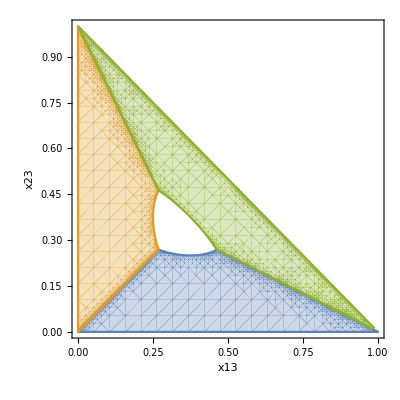

```mathematica
$Assumptions=0<eps<1 && 0<M<1 &&pm>0&&pp>0&& 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&u∈Reals&&u=!=0&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1/3&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>beta>0&&m∈Integers&&n∈Integers&&n≥0&&m≥0&&muMS>0&&1/3>tau>delta>0;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}];
expLogs[e_]:=e//.Log[a_/b_]:>Log[a]-Log[b]//.Log[a_*b_]:>Log[a]+Log[b]/.Log[a_^n_]:>  n*Log[a];


(* kinematics for p1m=0 *)
reg1kinematics[e_]:=e/.Vperp[p2]->-Vperp[q]/.Vperp[p1]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p2hatm->1-qhatm/.p2hatp->qhatp*qhatm/(1-qhatm)/.p1hatp->qhatm*(1-qhatp/(1-qhatm))/.p1hatm->0/.qhatp->x23*(1-qhatm)/.qhatm->x13/(1-x23);

(* kinematics for p2m=0 *)
reg2kinematics[e_]:=e/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p1hatm->1-qhatm/.p2hatp->(1-qhatp/(1-qhatm))/.p1hatp->qhatp*qhatm/(1-qhatm)/.p2hatm->0/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);

(* kinematics for qm=0 *)
reg3kinematics[e_]:=e/.Vperp[p2]->-Vperp[p1]/.Vperp[q]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p2hatm->1-p1hatm/.p2hatp->p1hatp*p1hatm/(1-p1hatm)/.qhatp->qhatm*(1-p1hatp/(1-p1hatm))/.qhatm->0/.p1hatp->(1-p1hatm)(1-x13/p1hatm)/.p1hatm->x13/(x13+x23);

(* options *)
onlyLO=False;
onlyNLO=False;
doCheckLeftoverIntegrals=False;

prefac=g^2*Cf;

phasespaceA=0;
phasespaceB=0;
phasespaceC=0;

(* 
  angularity definitions in the three regions of Dalitz-space 
*)
fA[x13_,x23_,a_]:=(x13 (x13+x23-1) (-x23/(x13 (x13+x23-1)))^(a/2)-x13 x23 (-(x13+x23-1)/(x13 x23))^(a/2))/(x13-1)
fB[x13_,x23_,a_]:=(x23 (x13+x23-1) (-x13/(x23 (x13+x23-1)))^(a/2)-x13 x23 (-(x13+x23-1)/(x13 x23))^(a/2))/(x23-1)
fC[x13_,x23_,a_]:=-((x13+x23-1) (x23 (-x13/(x23 (x13+x23-1)))^(a/2)+x13 (-x23/(x13 (x13+x23-1)))^(a/2)))/(x13+x23)
(* plot the thing *)
tautau=0.5;
aa=1;
RegionPlot[{2x13+x23<1&&x13+x23<1&&x23>x13&&0<fA[x13,x23,aa]<tautau,x13+2x23<1&&x13+x23<1&&x13>x23&&0<fB[x13,x23,aa]<tautau,2x13+x23>1&&x13+2x23>1&&x13+x23<1&&0<fC[x13,x23,aa]<tautau},{x23,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->5]
```

## Expressions for Integration Regions

### Phase Space Integrals

#### A -- Sideways Integration (x-first)

```mathematica
(* try integrating x first, then y *)

(*
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y}];
regAs2=Integrate[%*y^(m-1+eps),{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
*)

(* it worked but the output is HUGE! Almost 57000 terms long *)

(* instead of keeping the huge result, we'll store the 4x4 {n,m} elements that are necessary for usual calculations *)
(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regA00=-Pi^2/6+1/(2*ϵ^2)-2*τ-Log[τ]^2/2; 
regA01=τ*(1-Log[τ]);
regA02=0;
regA03=0;

regA10=-2+ϵ^(-1)-3*τ+Log[τ];
regA11=τ;
regA12=0;
regA13=0;

regA20=-1+1/(2*ϵ)-2*τ+Log[τ]/2;
regA21=τ/2;
regA22=0;
regA23=0;

regA30=-13/18+1/(3*ϵ)-2*τ+Log[τ]/3;
regA31=τ/3;
regA32=0;
regA33=0;
```

```mathematica
(*
Integrate[x^(0-1+eps)(1-x-y)^(eps),{x,y,1-2*y}]
Integrate[%*y^(0-1+eps),{y,0,tau}]
Series[%,{tau,0,4}]//Normal

Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
*)
```

#### B -- Vertical Integration (y-first)

```mathematica
(* summary *)

regB00=regA00;
regB01=regA10;
regB02=regA20;
regB03=regA30;

regB10=regA01;
regB11=regA11;
regB12=regA21;
regB13=regA31;

regB20=regA02;
regB21=regA12;
regB22=regA22;
regB23=regA32;

regB30=regA03;
regB31=regA13;
regB32=regA23;
regB33=regA33;
```

```mathematica
(*
Integrate[y^(m-1+eps)(1-x-y)^(eps),{y,x,1-2*x}]
Integrate[%*x^(n-1+eps),{x,0,tau}]
regBlong=Series[%,{tau,0,2}]//Normal
*)

(* this is equivalent to the region A integration, but with n interchanged with m *)
```

#### C -- Sideways Integration (x-first)

```mathematica
(* summary *)

(* it looks like I only need to know the result for c02, c11, and c20, so let's just do those *)

(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regC00=τ*(2-2*Log[τ]);
regC01=τ-τ*Log[τ];
regC02=-(τ*Log[τ]);
regC03=τ*(-1/2-Log[τ]);

regC10=τ*(1-Log[τ]);
regC11=τ;
regC12=τ/2;
regC13=τ/3;

regC20=-(τ*Log[τ]);
regC21=τ/2;
regC22=τ/6;
regC23=τ/12;

regC30=-(τ*(1+2*Log[τ]))/2;
regC31=τ/3;
regC32=τ/12;
regC33=τ/30;
```

```mathematica
(* convert integrals from y to u=1-x-y *)
(* then the integration region has the same form as region A so we can try the sideways integration again *)

(*nn=1;
mm=1;

regCs02i=Integrate[x^(nn-1+eps)(1-x-u)^(mm-1+eps),{x,u,1-2*u}]

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2]

regCs02ii=Integrate[%*u^eps,{u,0,tau}]
regCs02=Series[%,{tau,0,2}];
regCs02=Series[%,{tau,0,1}]//Normal;
regCs02=Series[%,{eps,0,0}]//Normal
regCsnnmm=Series[%,{tau,0,1}]//Normal
regCsnnmm//InputForm*)
```

#### Overall

```mathematica
int00=regA00+regB00+regC00;
int01=regA01+regB01+regC01;
int02=regA02+regB02+regC02;
int03=regA03+regB03+regC03;

int10=regA10+regB10+regC10;
int11=regA11+regB11+regC11;
int12=regA12+regB12+regC12;
int13=regA13+regB13+regC13;

int20=regA20+regB20+regC20;
int21=regA21+regB21+regC21;
int22=regA22+regB22+regC22;
int23=regA23+regB23+regC23;

int30=regA30+regB30+regC30;
int31=regA31+regB31+regC31;
int32=regA32+regB32+regC32;
int33=regA33+regB33+regC33;
```

## Subsubleading Order

### Contributions from A-type operators

#### Do the Dirac Algebra

```mathematica
(* leading order amplitude *)
ampA0=-I*g*Ta*SpinorUBar[p1].(  (2*FVD[p1,alpha]+GAD[alpha].GSD[q])/(2*SPD[p1,q])-FVD[nb,alpha]/SPD[nb,q]).Phatnb.GAD[mu].Phatnb.SpinorV[p2]//DeltaDef
ampA0dag=I*g*Tb*SpinorVBar[p2].Phatn.GAD[mu].Phatn.(  (2*FVD[p1,alpha]+GSD[q].GAD[alpha])/(2*SPD[p1,q])-FVD[nb,alpha]/SPD[nb,q]).SpinorU[p1]//DeltaDef

(* subleading order amplitude *)
ampA1=-I*g*Ta*SpinorUBar[p1].(Vperp[GAD[beta]].(GSD[nb]/2).GAD[mu].Phatnb-Phatnb.GAD[mu].(GSD[n]/2).Vperp[GAD[beta]]).SpinorV[p2]*Deltabarq[alpha,beta]/Q//DeltaDef
ampA1dag=I*g*Tb*SpinorVBar[p2].(Phatn.GAD[mu].(GSD[nb]/2).Vperp[GAD[rho]]-Vperp[GAD[rho]].(GSD[n]/2).GAD[mu].Phatn).SpinorU[p1]*Deltabarq[alpha,rho]/Q//DeltaDef

(* subleading order amplitude *)
ampA2=I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].Phatnb.Vperp[GAD[beta]].Vperp[GAD[gamma]]/qm+Vperp[GAD[beta]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[gamma]]/p1m).SpinorV[p2]*FVD[q,beta]*Deltabarq[alpha,gamma]/Q//DeltaDef
ampA2dag=-I*g*Tb*SpinorVBar[p2].(Vperp[GAD[sigma]].Vperp[GAD[rho]].Phatn.GAD[mu].Phatn/qm+Vperp[GAD[sigma]].(GSD[n]/2).GAD[mu].(GSD[nb]/2).Vperp[GAD[rho]]/p1m).SpinorU[p1]*FVD[q,rho]*Deltabarq[alpha,sigma]/Q//DeltaDef


ampAtot=(ampA0+lambda*ampA1+lambda^2*ampA2)/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a
ampAdagtot=(ampA0dag+lambda*ampA1dag+lambda^2*ampA2dag)/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a
ampAsqrtot=(Phatnb+Phatn).ampAdagtot.ampAtot.(Phatnb+Phatn)
%//Contract//DiracSimplify//FCE
ampAsqrtot=%/.SpinorU[p1].SpinorUBar[p1]->GSD[p1]/.SpinorVBar[p2]->GSD[p2]/.a_ .SpinorV[p2].b_:>a.b/.a_ .SpinorV[p2]:>a//DeltaDef//DiracSimplify//FCE
ampAsqrtruncLO=Series[ampAsqrtot,{lambda,0,0}]//Normal
evalthis=%;
If[!onlyLO,
ampAsqrtruncSSLO=Series[ampAsqrtot,{lambda,0,2}]//Normal;
evalthis=ampAsqrtruncSSLO;
]
If[onlyNLO,
ampAsqrtruncSSLO=Series[ampAsqrtot,{lambda,0,2}]//Normal;
evalthis=ampAsqrtruncSSLO-ampAsqrtruncLO;
]
evalthis//myPrint
evalthis/.Ta*Tb->Cf/.lambda->1/.Vperp[p2]->-Vperp[p1]-Vperp[q]//PhatDef//lcCompAll
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE
FullSimplify[%,TransformationFunctions->simplifList,TimeConstraint->{5,timeLimit}]
%//PhatDef//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft//contractPerpSandwichD;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft//contractPerpSandwichD;
%//contractPerpSandwichD//DiracSimplify//FCE;
%/.Vperp[GAD[a_]].GSD[Vperp[b_]].Vperp[GAD[a_]]:>(2-d)GSD[Vperp[b]]/.d->D-2//shiftPastPerpLeft
%//contractPerpSandwichD//DiracSimplify//FCE
FullSimplify[%,TimeConstraint->{5,timeLimit}]

%/.p1m->Q-qm/.p2p->Q(1-qp/p1m)/.p1p->qp*qm/(Q-qm)//FullSimplify
%/.p1m->Q-qm/.p2p->Q(1-qp/p1m)/.p1p->qp*qm/(Q-qm)//FullSimplify
endA=FullSimplify[%/.qm->qhatm*Q/.p1m->p1hatm*Q/.p2m->Q*p2hatm/.qp->Q*qhatp/.p1p->Q*p1hatp/.p2p->Q*p2hatp,TimeConstraint->{5,timeLimit}]

(* ---------------- *)

(* taking the dirac trace *)
endA/.p1hatm->1-qhatm/.GSD[nb].GSD[n].Vperp[GAD[mu]].Vperp[GAD[nu]]->SPD[n,nb]*4*Vperp[MTD[mu,nu]]/.GSD[nb].GSD[n]->2*4/.D->4-2*eps (* interestingly, you dont do the trace in D dimensions *)
%/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13)//FullSimplify
Series[%,{eps,0,1}]//Normal
%/.x23->1-x1/.x13->1-x2//Simplify
Series[%,{eps,0,1}]//Normal
krabbyA=%/.x1->1-x23/.x2->1-x13
```

-ⅈ g T^a ū(p_1).((2 p_1^α+γ^α.(γ·q))/(2 p_1·q)-(n̄)^α/q^-).(P̂)_(n̄).γ^μ.(P̂)_(n̄).v(p_2)

ⅈ g T^b v̄(p_2).(P̂)_n.γ^μ.(P̂)_n.((2 p_1^α+(γ·q).γ^α)/(2 p_1·q)-(n̄)^α/q^-).u(p_1)

-(ⅈ g T^a (g^αβ-((n̄)^α q^β)/q^-) ū(p_1).((γ^β)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)-(P̂)_(n̄).γ^μ.(γ·n)/2.(γ^β)_⊥).v(p_2))/Q

(ⅈ g T^b (g^αρ-((n̄)^α q^ρ)/q^-) v̄(p_2).((P̂)_n.γ^μ.(γ·n̄)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n)/2.γ^μ.(P̂)_n).u(p_1))/Q

(ⅈ g T^a q^β (g^αγ-((n̄)^α q^γ)/q^-) ū(p_1).(((γ^β)_⊥.(γ·n̄)/2.γ^μ.(γ·n)/2.(γ^γ)_⊥)/p_1^-+((P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^β)_⊥.(γ^γ)_⊥)/q^-).v(p_2))/Q

-(ⅈ g T^b q^ρ (g^ασ-((n̄)^α q^σ)/q^-) v̄(p_2).(((γ^σ)_⊥.(γ·n)/2.γ^μ.(γ·n̄)/2.(γ^ρ)_⊥)/p_1^-+((γ^σ)_⊥.(γ^ρ)_⊥.(P̂)_n.γ^μ.(P̂)_n)/q^-).u(p_1))/Q

-(ⅈ g λ T^a (g^αβ-((n̄)^α q^β)/q^-) (γ·p_1).((γ^β)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)-(P̂)_(n̄).γ^μ.(γ·n)/2.(γ^β)_⊥))/Q+(ⅈ g λ^2 T^a q^β (g^αγ-((n̄)^α q^γ)/q^-) (γ·p_1).(((γ^β)_⊥.(γ·n̄)/2.γ^μ.(γ·n)/2.(γ^γ)_⊥)/p_1^-+((P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^β)_⊥.(γ^γ)_⊥)/q^-))/Q-ⅈ g T^a (γ·p_1).((2 p_1^α+γ^α.(γ·q))/(2 p_1·q)-(n̄)^α/q^-).(P̂)_(n̄).γ^μ.(P̂)_(n̄)

(ⅈ g λ T^b (g^αρ-((n̄)^α q^ρ)/q^-) (γ·p_2).((P̂)_n.γ^μ.(γ·n̄)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n)/2.γ^μ.(P̂)_n))/Q-(ⅈ g λ^2 T^b q^ρ (g^ασ-((n̄)^α q^σ)/q^-) (γ·p_2).(((γ^σ)_⊥.(γ·n)/2.γ^μ.(γ·n̄)/2.(γ^ρ)_⊥)/p_1^-+((γ^σ)_⊥.(γ^ρ)_⊥.(P̂)_n.γ^μ.(P̂)_n)/q^-))/Q+ⅈ g T^b (γ·p_2).(P̂)_n.γ^μ.(P̂)_n.((2 p_1^α+(γ·q).γ^α)/(2 p_1·q)-(n̄)^α/q^-)

((P̂)_n+(P̂)_(n̄)).((ⅈ g λ T^b (g^αρ-((n̄)^α q^ρ)/q^-) (γ·p_2).((P̂)_n.γ^μ.(γ·n̄)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n)/2.γ^μ.(P̂)_n))/Q-(ⅈ g λ^2 T^b q^ρ (g^ασ-((n̄)^α q^σ)/q^-) (γ·p_2).(((γ^σ)_⊥.(γ·n)/2.γ^μ.(γ·n̄)/2.(γ^ρ)_⊥)/p_1^-+((γ^σ)_⊥.(γ^ρ)_⊥.(P̂)_n.γ^μ.(P̂)_n)/q^-))/Q+ⅈ g T^b (γ·p_2).(P̂)_n.γ^μ.(P̂)_n.((2 p_1^α+(γ·q).γ^α)/(2 p_1·q)-(n̄)^α/q^-)).(-(ⅈ g λ T^a (g^αβ-((n̄)^α q^β)/q^-) (γ·p_1).((γ^β)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)-(P̂)_(n̄).γ^μ.(γ·n)/2.(γ^β)_⊥))/Q+(ⅈ g λ^2 T^a q^β (g^αγ-((n̄)^α q^γ)/q^-) (γ·p_1).(((γ^β)_⊥.(γ·n̄)/2.γ^μ.(γ·n)/2.(γ^γ)_⊥)/p_1^-+((P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^β)_⊥.(γ^γ)_⊥)/q^-))/Q-ⅈ g T^a (γ·p_1).((2 p_1^α+γ^α.(γ·q))/(2 p_1·q)-(n̄)^α/q^-).(P̂)_(n̄).γ^μ.(P̂)_(n̄)).((P̂)_n+(P̂)_(n̄))

-(D g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·n).(γ^γ)_⊥.(P̂)_n g^αγ g^ασ q^+ q^- λ^4)/(2 Q^2 p_1^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·n).(γ^γ)_⊥.(P̂)_n g^αγ g^ασ q^+ q^- λ^4)/(Q^2 p_1^-)-(D g^2 T^a 4 q^+ q^- λ^4)/(2 Q^2 p_1^-)+679
 |  |  |  |

-(D g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·n).(γ^σ)_⊥.(P̂)_n q^+ q^- λ^4)/(2 Q^2 p_1^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·n).(γ^σ)_⊥.(P̂)_n q^+ q^- λ^4)/(Q^2 p_1^-)-(D g^2 T^a 20^b 1 q^+ q^- λ^4)/(2 Q^2 p_1^-)+351
 |  |  |  |

1/(2 q^- p_1·q)(-D g^2 q^- T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-D g^2 q^- T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-D g^2 q^- T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-D g^2 q^- T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n+g^2 (-T^a) T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-g^2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-g^2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-g^2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-g^2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n+2 g^2 q^- T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄)+2 g^2 q^- T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄)+2 g^2 q^- T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n+2 g^2 q^- T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-4 g^2 p_1^- T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-4 g^2 p_1^- T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-4 g^2 p_1^- T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-4 g^2 p_1^- T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n)

evalthis=((T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(4 Q p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(4 Q p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_n g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_(n̄) g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_n g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_(n̄) g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^σ)_⊥.(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ^γ)_⊥.(P̂)_n g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ^γ)_⊥.(P̂)_(n̄) g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ^γ)_⊥.(P̂)_n g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(γ·n).(γ^γ)_⊥.(P̂)_(n̄) g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^σ)_⊥.(γ·n).γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(8 Q p_1^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·q).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·q).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^- p_1·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·q).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·q).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^- p_1·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·p_1_⊥).(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_1_⊥).(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ·p_1_⊥).(P̂)_n g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ·p_1_⊥).(P̂)_(n̄) g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·p_1_⊥).(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ·p_1_⊥).(P̂)_n g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ·p_1_⊥).(P̂)_(n̄) g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_1_⊥).(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^σ)_⊥.(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ^σ)_⊥.(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^γ.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(P̂)_(n̄) g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^σ)_⊥.(γ·q_⊥).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).γ^σ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(2 Q q^- p_1·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2)/(2 Q q^- p_1·q)-(2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ p_1^- g^2)/(Q q^- p_1·q)-(2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ p_1^- g^2)/(Q q^- p_1·q)-(2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ p_1^- g^2)/(Q q^- p_1·q)-(2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ p_1^- g^2)/(Q q^- p_1·q)) λ^2+1/(4 Q q^- p_1·q)(T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2+T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) p_1^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_n q^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-2 T^a T^b (P̂)_n.(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_n q^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_1_⊥).(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_1_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) q^- g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) q^- g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^β)_⊥.(P̂)_n q^- g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^β)_⊥.(P̂)_(n̄) q^- g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^β)_⊥.(P̂)_n q^- g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^β)_⊥.(P̂)_(n̄) q^- g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).γ^β.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).γ^ρ.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2) λ+1/(2 q^- p_1·q)(-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-4 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-4 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_1^- g^2-4 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2-4 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_1^- g^2-D T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-D T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2-D T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2-D T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2)

(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)+(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)+146+(29+2 C_F 1 q^- g^2-C_F D 1 q^- g^2+2 C_F 1 q^- g^2-C_F D 1 q^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F 1 g^2+C_F 1 g^2+C_F 1 g^2+C_F 1 g^2+C_F 1 g^2+C_F 1 g^2+C_F 1 g^2+73+C_F 1 q^- g^2+C_F 1 q^- g^2-C_F 1 q^- g^2-C_F 1 q^- g^2-C_F 1 q^- g^2+C_F 1 q^- g^2+C_F 1 q^- g^2-C_F 1 q^- g^2)/(4 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))
 |  |  |  |

(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(16 Q^2)+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ g^2)/(16 Q^2)+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(16 Q^2)-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(32 Q^2)+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ g^2)/(128 Q^2)+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(128 Q^2)+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(128 Q^2)+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(64 Q^2)-(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- g^2)/(8 Q^2)-(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(4 Q^2)-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- g^2)/(64 Q^2)-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(64 Q^2)+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(64 Q^2)+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- g^2)/(64 Q^2)+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(64 Q^2)-(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(64 Q^2)+(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(16 Q^2)+(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(128 Q^2)-(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(8 Q^2)+(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^- p_2^- g^2)/(64 Q^2)+(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(64 Q^2)-(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(64 Q^2)-(C_F (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2 g^2)/(128 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2 g^2)/(128 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(128 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(128 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·q_⊥).(γ·n) p_2^+ g^2)/(16 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(64 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·q_⊥).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n̄).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·q_⊥).(γ·n) p_2^+ p_1^- g^2)/(4 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(16 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(16 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(32 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(32 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n) p_2^+ q^+ p_1^- g^2)/(16 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(4 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(64 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(512 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F D (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·q_⊥).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(64 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(64 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ·n) p_2^+ q^+ q^- g^2)/(Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n) p_2^+ q^+ q^- g^2)/(16 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- g^2)/(64 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- g^2)/(256 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- q^- g^2)/(128 Q (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- q^- g^2)/(256 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ q^- g^2)/(256 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- g^2)/(256 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- g^2)/(256 Q p_1^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·q_⊥).(γ·n) p_2^+ (p_1^-)^2 g^2)/(8 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(8 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ g^2)/(1024 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(1024 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(1024 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^- g^2)/(512 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(512 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(512 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(1024 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(512 Q q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))

FullSimplify::gtime: Returning the simplest form found in the allowed time of TraditionalForm`30.` seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

1/(256 Q^2 p_1^- q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))C_F g^2 (-64 Q^2 (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^3-64 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·q_⊥).(γ·n) p_2^+ (p_1^-)^3+16 Q (γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^3-16 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^3-16 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^3-64 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^3-32 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ q^- (p_1^-)^3-64 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^3-4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ q^- (p_1^-)^3-4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^3+4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^3+4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ q^- (p_1^-)^3+4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^3-4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^3-32 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- q^- (p_1^-)^3+4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) q^+ p_2^- q^- (p_1^-)^3+4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- q^- (p_1^-)^3-4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- q^- (p_1^-)^3+4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 (p_1^-)^2-4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ (q^-)^2 (p_1^-)^2-4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 (p_1^-)^2+4 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 (p_1^-)^2-4 Q (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 (p_1^-)^2-32 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2-64 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2-4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2-4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2+4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2+4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2+4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2-4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 (p_1^-)^2-64 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2 (p_1^-)^2-128 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 (p_1^-)^2-8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2 (p_1^-)^2-8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 (p_1^-)^2+8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 (p_1^-)^2+8 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2 (p_1^-)^2+8 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 (p_1^-)^2-8 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 (p_1^-)^2-4 Q (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- (q^-)^2 (p_1^-)^2-32 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^- (q^-)^2 (p_1^-)^2+4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^+ p_2^- (q^-)^2 (p_1^-)^2+4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^- (q^-)^2 (p_1^-)^2-4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^- (q^-)^2 (p_1^-)^2-64 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2 (p_1^-)^2+8 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) q^+ p_2^- (q^-)^2 (p_1^-)^2+8 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2 (p_1^-)^2-8 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2 (p_1^-)^2-4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ (p_1^-)^2-4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2-4 Q (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2-4 Q (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- (p_1^-)^2-64 Q^2 (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-128 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·q_⊥).(γ·n) p_2^+ q^- (p_1^-)^2+64 Q (γ·n̄).(γ^μ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2+32 Q (γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-32 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-16 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^- (p_1^-)^2-8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2+8 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-8 Q (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2+2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ q^- (p_1^-)^2-2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-2 Q (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- (p_1^-)^2-512 Q (γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+32 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n) p_2^+ q^+ q^- (p_1^-)^2-128 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+32 Q (γ·n̄).(γ·n).(γ^μ)_⊥.(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+64 (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ q^- (p_1^-)^2+64 (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+16 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2-8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ q^- (p_1^-)^2+8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+2 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ q^- (p_1^-)^2+4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^+ q^- (p_1^-)^2-8 Q (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- (p_1^-)^2-2 Q (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- (p_1^-)^2+16 (γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- q^- (p_1^-)^2+2 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- q^- (p_1^-)^2+4 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) (p_1^+)^2 p_2^+ (q^-)^2 p_1^--16 D Q^2 (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^-+32 Q^2 (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^--8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·q_⊥).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^--8 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^-+8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ (q^-)^2 p_1^-+8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^--2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ (q^-)^2 p_1^--2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^-+2 Q (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^--2 Q (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ (q^-)^2 p_1^-+64 (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^+ p_2^+ (q^-)^2 p_1^-+64 (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^-+16 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^-+4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^-+4 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^--8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^-+8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_1^+ p_2^+ (q^-)^2 p_1^-+8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^-+2 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ (q^-)^2 p_1^--512 Q (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+32 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+32 Q (γ·n̄).(γ·n).(γ^μ)_⊥.(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+128 (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2 p_1^-+128 (γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+32 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^--16 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+16 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2 p_1^-+16 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+4 (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 p_1^-+8 (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^+ (q^-)^2 p_1^-+2 Q (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- (q^-)^2 p_1^--2 Q (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- (q^-)^2 p_1^-+16 (γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^- (q^-)^2 p_1^-+2 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^- (q^-)^2 p_1^-+32 (γ·n).(γ^ρ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2 p_1^-+4 (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2 p_1^-+8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ p_1^-+8 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^-+2 Q (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^-+2 Q (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- p_1^--32 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·q_⊥).(γ·n) p_2^+ q^- p_1^-+8 Q (γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^--16 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^--4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·q_⊥).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^-+16 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^- p_1^-+16 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(P̂)_(n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^-+4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n).(γ·n̄) p_2^+ q^- p_1^-+4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n).(γ^β)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^-+4 Q (γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^--4 Q (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^--Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^- p_1^--Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^-+Q (γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^- p_1^-+8 Q (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^- p_1^-+2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^β)_⊥.(γ·n̄).(γ^β)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^- p_1^-+4 Q (γ·n).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- p_1^--4 Q (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- p_1^-+Q (γ·n).(γ^σ)_⊥.(γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^- q^- p_1^--4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^3-4 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^3-4 Q (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^3-4 Q (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^3-8 Q (γ·n̄).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2-2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n).(γ·n̄) p_2^+ q^+ (q^-)^2-2 Q (γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^γ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^γ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2-8 Q (γ·n).(γ^σ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) q^+ p_2^- (q^-)^2)

-(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(2 Q p_1^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(4 C_F (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(Q p_1^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(3 C_F D (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(Q p_1^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)+(C_F D (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(2 Q (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(Q (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(Q (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^- g^2)/(4 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F (γ·n̄).(γ·n) p_2^+ q^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)-(C_F D (γ·n̄).(γ·n) p_2^+ q^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)-(2 C_F (γ·n̄).(γ·n) p_1^+ p_2^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_1^+ p_2^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(4 C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(2 C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))

-(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(2 Q p_1^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(4 C_F (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(Q p_1^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(3 C_F D (γ·n̄).(γ·n) p_2^+ q^+ (q^-)^2 g^2)/(Q p_1^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)+(C_F D (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(2 Q (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(Q (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- g^2)/(Q (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^- g^2)/(4 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F (γ·n̄).(γ·n) p_2^+ q^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)-(C_F D (γ·n̄).(γ·n) p_2^+ q^- g^2)/(q^+ p_1^-+p_1^+ q^-+2 q^+ q^-)-(2 C_F (γ·n̄).(γ·n) p_1^+ p_2^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_1^+ p_2^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(4 C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(2 C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(Q^2 (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ q^+ (p_1^-)^2 g^2)/(Q q^- (q^+ p_1^-+p_1^+ q^-+2 q^+ q^-))

((D-2) g^2 p_2^+ C_F ((D-2) p_1^- (q^-)^2 Q^2+2 (p_1^-)^2 q^- (Q ((D-2) q^++2 Q)+2 q^- (p_1^++2 q^+))+2 (D-4) q^+ (q^-)^3 Q+4 (p_1^-)^3 (q^+ (q^-+Q)+Q^2)) (γ·n̄).(γ·n))/(4 p_1^- q^- Q^2 (p_1^+ q^-+q^+ (p_1^-+2 q^-)))

-((D-2) g^2 C_F (q^+-p_1^-) (Q (Q-q^-) ((D-2) (q^-)^2-4 q^- Q+4 Q^2)+2 q^+ (q^- (2 (D-4) q^- (q^--Q)+(D-6) Q^2)+2 Q^3)) (γ·n̄).(γ·n))/(4 p_1^- q^+ q^- Q^2)

-((D-2) g^2 C_F (q^++q^--Q) (Q (Q-q^-) ((D-2) (q^-)^2-4 q^- Q+4 Q^2)+2 q^+ (q^- (2 (D-4) q^- (q^--Q)+(D-6) Q^2)+2 Q^3)) (γ·n̄).(γ·n))/(4 q^+ q^- Q^2 (Q-q^-))

((D-2) g^2 ((q̂)^++(q̂)^--1) C_F ((q̂)^- ((q̂)^- (-(D-2) (q̂)^-+D+2)-8)+2 (q̂)^+ ((q̂)^- (2 (D-4) ((q̂)^--1) (q̂)^-+D-6)+2)+4) (γ·n̄).(γ·n))/(4 (q̂)^+ ((q̂)^--1) (q̂)^-)

(2 g^2 ((q̂)^++(q̂)^--1) (2-2 ϵ) C_F ((q̂)^- ((q̂)^- (-(q̂)^- (2-2 ϵ)-2 ϵ+6)-8)+2 (q̂)^+ ((q̂)^- (-4 ((q̂)^--1) (q̂)^- ϵ-2 ϵ-2)+2)+4))/((q̂)^+ ((q̂)^--1) (q̂)^-)

-(8 g^2 (ϵ-1) C_F ((x13-1) (2 (x13^2-1) x23+2 (x13+1) (x13-1)^2+x23^2)+x23 ϵ (x13 (2 x13^2+4 x13 (x23-1)+x23 (4 x23-5)+2)+x23)))/((x13-1) x13 x23)

(8 g^2 C_F (2 (x13^2-1) x23+2 (x13+1) (x13-1)^2+x23^2))/(x13 x23)-(16 g^2 ϵ C_F (x13^4-2 x13^3-2 x13^2 x23^2+x13^2 x23-2 x13 x23^3+3 x13 x23^2-2 x13 x23+2 x13-x23^2+x23-1))/((x13-1) x13 x23)

(8 g^2 C_F (-2 x2^3 (x1+2 ϵ-3)-2 (x1-1) x2^2 ((2 x1-1) ϵ-2)-(x1-1)^2 x2 ((4 x1-6) ϵ-1)+4 (x1-1)^3 ϵ+2 x2^4 (ϵ-1)))/((x1-1) (x2-1) x2)

(8 g^2 C_F (x1^2-2 x1 x2^2+4 x1 x2-2 x1-2 x2^3+6 x2^2-4 x2+1))/((x1-1) (x2-1))+(8 g^2 ϵ C_F (-2 (x1-1) (2 x1-1) x2^2+(6-4 x1) (x1-1)^2 x2+4 (x1-1)^3+2 x2^4-4 x2^3))/((x1-1) (x2-1) x2)

(8 g^2 ϵ C_F ((1-x13) (6-4 (1-x23)) x23^2+2 (1-x13)^2 (2 (1-x23)-1) x23+2 (1-x13)^4-4 (1-x13)^3-4 x23^3))/((1-x13) x13 x23)+(8 g^2 C_F (-2 (1-x13)^2 (1-x23)+4 (1-x13) (1-x23)-2 (1-x13)^3+6 (1-x13)^2-4 (1-x13)+(1-x23)^2-2 (1-x23)+1))/(x13 x23)

```mathematica
endA/.SPD[p1,q]->x13*Q^2/2//gPerpDef//Simplify
Tr[%]//FCE
%/.p2hatp->x2-p2hatm/.p1hatm->1-qhatm-p2hatm
%/.p2hatm->x2(1-mu)/2
%//Expand
```

((D-2) g^2 ((q̂)^++(q̂)^--1) C_F ((q̂)^- ((q̂)^- (-(D-2) (q̂)^-+D+2)-8)+2 (q̂)^+ ((q̂)^- (2 (D-4) ((q̂)^--1) (q̂)^-+D-6)+2)+4) (γ·n̄).(γ·n))/(4 (q̂)^+ ((q̂)^--1) (q̂)^-)

(2 (D-2) g^2 ((q̂)^++(q̂)^--1) C_F ((q̂)^- ((q̂)^- (-(D-2) (q̂)^-+D+2)-8)+2 (q̂)^+ ((q̂)^- (2 (D-4) ((q̂)^--1) (q̂)^-+D-6)+2)+4))/((q̂)^+ ((q̂)^--1) (q̂)^-)

(2 (D-2) g^2 ((q̂)^++(q̂)^--1) C_F ((q̂)^- ((q̂)^- (-(D-2) (q̂)^-+D+2)-8)+2 (q̂)^+ ((q̂)^- (2 (D-4) ((q̂)^--1) (q̂)^-+D-6)+2)+4))/((q̂)^+ ((q̂)^--1) (q̂)^-)

(2 (D-2) g^2 ((q̂)^++(q̂)^--1) C_F ((q̂)^- ((q̂)^- (-(D-2) (q̂)^-+D+2)-8)+2 (q̂)^+ ((q̂)^- (2 (D-4) ((q̂)^--1) (q̂)^-+D-6)+2)+4))/((q̂)^+ ((q̂)^--1) (q̂)^-)

(8 D^2 g^2 ((q̂)^-)^3 C_F)/((q̂)^--1)-(2 D^2 g^2 ((q̂)^-)^3 C_F)/((q̂)^+ ((q̂)^--1))-(18 D^2 g^2 ((q̂)^-)^2 C_F)/((q̂)^--1)+(8 D^2 g^2 (q̂)^+ ((q̂)^-)^2 C_F)/((q̂)^--1)+(4 D^2 g^2 ((q̂)^-)^2 C_F)/((q̂)^+ ((q̂)^--1))+(14 D^2 g^2 (q̂)^- C_F)/((q̂)^--1)-(8 D^2 g^2 (q̂)^+ (q̂)^- C_F)/((q̂)^--1)-(2 D^2 g^2 (q̂)^- C_F)/((q̂)^+ ((q̂)^--1))-(4 D^2 g^2 C_F)/((q̂)^--1)+(4 D^2 g^2 (q̂)^+ C_F)/((q̂)^--1)-(48 D g^2 ((q̂)^-)^3 C_F)/((q̂)^--1)+(8 D g^2 ((q̂)^-)^3 C_F)/((q̂)^+ ((q̂)^--1))+(104 D g^2 ((q̂)^-)^2 C_F)/((q̂)^--1)-(48 D g^2 (q̂)^+ ((q̂)^-)^2 C_F)/((q̂)^--1)-(8 D g^2 ((q̂)^-)^2 C_F)/((q̂)^+ ((q̂)^--1))-(80 D g^2 (q̂)^- C_F)/((q̂)^--1)+(48 D g^2 (q̂)^+ (q̂)^- C_F)/((q̂)^--1)-(16 D g^2 (q̂)^- C_F)/((q̂)^+ ((q̂)^--1))+(24 D g^2 C_F)/((q̂)^--1)-(32 D g^2 (q̂)^+ C_F)/((q̂)^--1)+(24 D g^2 C_F)/((q̂)^+ ((q̂)^--1))+(8 D g^2 (q̂)^+ C_F)/(((q̂)^--1) (q̂)^-)-(8 D g^2 C_F)/((q̂)^+ ((q̂)^--1) (q̂)^-)+(64 g^2 ((q̂)^-)^3 C_F)/((q̂)^--1)-(8 g^2 ((q̂)^-)^3 C_F)/((q̂)^+ ((q̂)^--1))-(136 g^2 ((q̂)^-)^2 C_F)/((q̂)^--1)+(64 g^2 (q̂)^+ ((q̂)^-)^2 C_F)/((q̂)^--1)+(104 g^2 (q̂)^- C_F)/((q̂)^--1)-(64 g^2 (q̂)^+ (q̂)^- C_F)/((q̂)^--1)+(40 g^2 (q̂)^- C_F)/((q̂)^+ ((q̂)^--1))-(32 g^2 C_F)/((q̂)^--1)+(48 g^2 (q̂)^+ C_F)/((q̂)^--1)-(48 g^2 C_F)/((q̂)^+ ((q̂)^--1))-(16 g^2 (q̂)^+ C_F)/(((q̂)^--1) (q̂)^-)+(16 g^2 C_F)/((q̂)^+ ((q̂)^--1) (q̂)^-)

#### Integrate Over A’s phase space

```mathematica
krabbyA=krabbyA/.p1hatm->1-qhatm/.GSD[nb].GSD[n].Vperp[GAD[mu]].Vperp[GAD[nu]]->2*4*Vperp[MTD[mu,nu]]/.eps->negeps/.negeps->-eps

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
A00=SeriesCoefficient[krabbyA*x13*x23,{x23,0,0},{x13,0,0}];
A10=SeriesCoefficient[krabbyA*x13*x23,{x23,0,1},{x13,0,0}];
A20=SeriesCoefficient[krabbyA*x13*x23,{x23,0,2},{x13,0,0}];
A30=SeriesCoefficient[krabbyA*x13*x23,{x23,0,3},{x13,0,0}];

A01=SeriesCoefficient[krabbyA*x13*x23,{x23,0,0},{x13,0,1}];
A11=SeriesCoefficient[krabbyA*x13*x23,{x23,0,1},{x13,0,1}];
A21=SeriesCoefficient[krabbyA*x13*x23,{x23,0,2},{x13,0,1}];
A31=SeriesCoefficient[krabbyA*x13*x23,{x23,0,3},{x13,0,1}];

A02=SeriesCoefficient[krabbyA*x13*x23,{x23,0,0},{x13,0,2}];
A12=SeriesCoefficient[krabbyA*x13*x23,{x23,0,1},{x13,0,2}];
A22=SeriesCoefficient[krabbyA*x13*x23,{x23,0,2},{x13,0,2}];
A32=SeriesCoefficient[krabbyA*x13*x23,{x23,0,3},{x13,0,2}];

A03=SeriesCoefficient[krabbyA*x13*x23,{x23,0,0},{x13,0,3}];
A13=SeriesCoefficient[krabbyA*x13*x23,{x23,0,1},{x13,0,3}];
A23=SeriesCoefficient[krabbyA*x13*x23,{x23,0,2},{x13,0,3}];
A33=SeriesCoefficient[krabbyA*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrA={{A00,A01,A02,A03},{A10,A11,A12,A13},{A20,A21,A22,A23},{A30,A31,A32,A33}}
checksumA=krabbyA*x13*x23-({1,x23,x23^2,x23^3}.coeffArrA.{1,x13,x13^2,x13^3})//FullSimplify
leftoverIntegralA=0;
```

(8 g^2 C_F (-2 (1-x13)^2 (1-x23)+4 (1-x13) (1-x23)-2 (1-x13)^3+6 (1-x13)^2-4 (1-x13)+(1-x23)^2-2 (1-x23)+1))/(x13 x23)-(8 g^2 ϵ C_F ((1-x13) (6-4 (1-x23)) x23^2+2 (1-x13)^2 (2 (1-x23)-1) x23+2 (1-x13)^4-4 (1-x13)^3-4 x23^3))/((1-x13) x13 x23)

(16 C_F g^2+16 C_F ϵ g^2 | -16 C_F g^2-16 C_F ϵ g^2 | -16 C_F g^2-16 C_F ϵ g^2 | 16 C_F g^2+16 C_F ϵ g^2
-16 C_F g^2-16 C_F ϵ g^2 | 16 C_F g^2 ϵ | 16 C_F g^2 | 0
8 C_F g^2+16 C_F ϵ g^2 | -32 C_F g^2 ϵ | 0 | 0
0 | 32 C_F g^2 ϵ | 32 C_F g^2 ϵ | 32 C_F g^2 ϵ)

-(32 g^2 x13^4 x23^3 ϵ C_F)/(x13-1)

```mathematica
If[doCheckLeftoverIntegrals,

leftoverStuffA=checksumA/(x13*x23)/.x23->x/.x13->y;

Integrate[leftoverStuffA*x^eps*(1-x-y)^(eps),{x,y,1-2*y}];

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2];

Integrate[%*y^(eps),{y,0,tau}];
Series[%,{tau,0,2}]//Normal;
Series[%,{tau,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
leftoverIntegralA=Series[%,{tau,0,1}]//Normal;
]
```

```mathematica
(* contribution from region A *)

totalA=leftoverIntegralA;
totalA+=A00*regA00+A01*regA01+A02*regA02+A03*regA03;
totalA+=A10*regA10+A11*regA11+A12*regA12+A13*regA13;
totalA+=A20*regA20+A21*regA21+A22*regA22+A23*regA23;
totalA+=A30*regA30+A31*regA31+A32*regA32+A33*regA33;
totalA=totalA//FullSimplify
Series[%,{eps,0,0}]//Normal
```

(4 g^2 C_F (-3 ϵ^2 log(τ) (-4 τ (ϵ+1)+2 (ϵ+1) log(τ)+2 ϵ+3)-ϵ (2 ϵ (6 τ+8 τ ϵ+(π^2-6) (ϵ+1))+3)+6))/(3 ϵ^2)

4/3 g^2 C_F (-12 τ-6 log^2(τ)+12 τ log(τ)-9 log(τ)-2 π^2+12)+(8 g^2 C_F)/ϵ^2-(4 g^2 C_F)/ϵ

#### Summarize

```mathematica
(* testing how it should be done *)

Series[totalA/.eps->negeps/.negeps->-eps,{tau,0,1}]//Normal
Series[%,{eps,0,1}]//Normal//FullSimplify
phasespaceA=Series[%,{eps,0,1}]//Normal
```

-8 g^2 C_F log^2(τ)-12 g^2 C_F log(τ)+(8 g^2 C_F)/ϵ^2+8 g^2 ϵ C_F log^2(τ)+8 g^2 ϵ C_F log(τ)+τ (16 g^2 C_F log(τ)-16 g^2 ϵ C_F log(τ)+64/3 g^2 ϵ C_F-16 g^2 C_F)-16 g^2 ϵ C_F+8/3 π^2 g^2 ϵ C_F+(4 g^2 C_F)/ϵ+16 g^2 C_F-8/3 π^2 g^2 C_F

(4 g^2 C_F (3 ϵ^2 log(τ) (4 τ+(2-4 τ) ϵ+2 (ϵ-1) log(τ)-3)+ϵ (2 ϵ (-6 τ+8 τ ϵ+(π^2-6) (ϵ-1))+3)+6))/(3 ϵ^2)

4/3 g^2 C_F (-12 τ-6 log^2(τ)+12 τ log(τ)-9 log(τ)-2 π^2+12)+(8 g^2 C_F)/ϵ^2+8/3 g^2 ϵ C_F (8 τ+3 log^2(τ)-6 τ log(τ)+3 log(τ)+π^2-6)+(4 g^2 C_F)/ϵ

```mathematica
(* correct at LO *)(* but only for integration over region A *)
(* 4/3 g^2 Subscript[C, F] (-6 log^2(τ)-9 log(τ)-2 π^2+12)+(8 g^2 Subscript[C, F])/ϵ^2+8/3 g^2 ϵ Subscript[C, F] (6 τ+3 log^2(τ)+3 log(τ)+π^2-6)+(4 g^2 Subscript[C, F])/ϵ *)
```

### Contributions from B-type operators

#### Do the Dirac Algebra

```mathematica
phasespaceB=0;

(* leading order amplitude *)
ampB0=I*g*Ta*SpinorUBar[p1].Phatnb.GAD[mu].Phatnb.(  (2*FVD[p2,alpha]+GSD[q].GAD[alpha])/(2*SPD[p2,q])-FVD[n,alpha]/SPD[n,q]).SpinorV[p2]//DeltaDef
ampB0dag=-I*g*Tb*SpinorVBar[p2].(  (2*FVD[p2,alpha]+GAD[alpha].GSD[q])/(2*SPD[p2,q])-FVD[n,alpha]/SPD[n,q]).Phatn.GAD[mu].Phatn.SpinorU[p1]//DeltaDef

(* subleading order amplitude *)
ampB1=I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].(GSD[n]/2).Vperp[GAD[rho]]-Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].Phatnb).SpinorV[p2]*Deltaq[alpha,rho]/Q//DeltaDef
ampB1dag=-I*g*Tb*SpinorVBar[p2].(Vperp[GAD[beta]].(GSD[n]/2).GAD[mu].Phatn-Phatn.GAD[mu].(GSD[nb]/2).Vperp[GAD[beta]]).SpinorU[p1]*Deltaq[alpha,beta]/Q//DeltaDef

(* subleading order amplitude *)
ampB2=-I*g*Ta*SpinorUBar[p1].(Vperp[GAD[sigma]].Vperp[GAD[rho]].Phatnb.GAD[mu].Phatnb/qp+Vperp[GAD[sigma]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[rho]]/p2p).SpinorV[p2]*FVD[q,rho]*Deltaq[alpha,sigma]/Q//DeltaDef
ampB2dag=I*g*Tb*SpinorVBar[p2].(Phatn.GAD[mu].Phatn.Vperp[GAD[beta]].Vperp[GAD[gamma]]/qp+Vperp[GAD[beta]].(GSD[n]/2).GAD[mu].(GSD[nb]/2).Vperp[GAD[gamma]]/p2p).SpinorU[p1]*FVD[q,beta]*Deltaq[alpha,gamma]/Q//DeltaDef

ampBtot=(ampB0+lambda*ampB1+lambda^2*ampB2)/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a
ampBdagtot=(ampB0dag+lambda*ampB1dag+lambda^2*ampB2dag)/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a
ampBsqrtot=(Phatnb+Phatn).ampBdagtot.ampBtot.(Phatnb+Phatn)
%//Contract//DiracSimplify//FCE
ampBsqrtot=%/.SpinorU[p1].SpinorUBar[p1]->GSD[p1]/.SpinorVBar[p2]->GSD[p2]/.a_ .SpinorV[p2].b_:>a.b/.a_ .SpinorV[p2]:>a//DeltaDef//DiracSimplify//FCE
ampBsqrtruncLO=Series[ampBsqrtot,{lambda,0,0}]//Normal
evalthis=%;
If[!onlyLO,
ampBsqrtruncSSLO=Series[ampBsqrtot,{lambda,0,2}]//Normal;
evalthis=ampBsqrtruncSSLO;
]
If[onlyNLO,
ampBsqrtruncSSLO=Series[ampBsqrtot,{lambda,0,2}]//Normal;
evalthis=ampBsqrtruncSSLO-ampBsqrtruncLO;
]

evalthis//myPrint
evalthis/.Ta*Tb->Cf/.lambda->1//PhatDef//lcCompAll

%/.Vperp[p2]->-Vperp[q]/.Vperp[p1]->0//Contract//DiracSimplify//FCE
FullSimplify[%,TimeConstraint->{5,timeLimit}]
%//PhatDef//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft//contractPerpSandwichD;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft;
%//DiracSimplify//FCE;
%//shiftPastPerpLeft//contractPerpSandwichD;
%//contractPerpSandwichD//DiracSimplify//FCE;
%/.Vperp[GAD[a_]].GSD[Vperp[b_]].Vperp[GAD[a_]]:>(2-d)GSD[Vperp[b]]/.d->D-2//shiftPastPerpLeft
%//contractPerpSandwichD//DiracSimplify//FCE
Tr[%]//FCE
FullSimplify[%,TimeConstraint->{5,timeLimit}]

%/.p2p->Q-qp/.p1m->Q(1-qm/p2p)/.p2m->qm*qp/(Q-qp)//FullSimplify
%/.p2p->Q-qp/.p1m->Q(1-qm/p2p)/.p2m->qm*qp/(Q-qp)//FullSimplify
endB=FullSimplify[%/.qm->qhatm*Q/.p2p->p2hatp*Q/.p2m->p2hatm*Q/.qp->Q*qhatp,TimeConstraint->{5,timeLimit}]

(* ---------------- *)

(* taking the dirac trace *)
endB/.p2hatp->1-qhatp/.GSD[nb].GSD[n].Vperp[GAD[mu]].Vperp[GAD[nu]]->SPD[n,nb]*4*Vperp[MTD[mu,nu]]/.GSD[nb].GSD[n]->2*4/.D->4-2*eps (* interestingly, you dont do the trace in D dimensions *)
%/.qhatm->x23*(1-qhatp)/.qhatp->x13/(1-x23)//FullSimplify
Series[%,{eps,0,1}]//Normal
%/.x23->1-x1/.x13->1-x2//Simplify
Series[%,{eps,0,1}]//Normal
krabbyB=%/.x1->1-x23/.x2->1-x13
```

ⅈ g T^a ū(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).((2 p_2^α+(γ·q).γ^α)/(2 p_2·q)-n^α/q^+).v(p_2)

-ⅈ g T^b v̄(p_2).((2 p_2^α+γ^α.(γ·q))/(2 p_2·q)-n^α/q^+).(P̂)_n.γ^μ.(P̂)_n.u(p_1)

(ⅈ g T^a (g^αρ-(n^α q^ρ)/q^+) ū(p_1).((P̂)_(n̄).γ^μ.(γ·n)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)).v(p_2))/Q

-(ⅈ g T^b (g^αβ-(n^α q^β)/q^+) v̄(p_2).((γ^β)_⊥.(γ·n)/2.γ^μ.(P̂)_n-(P̂)_n.γ^μ.(γ·n̄)/2.(γ^β)_⊥).u(p_1))/Q

-(ⅈ g T^a q^ρ (g^ασ-(n^α q^σ)/q^+) ū(p_1).(((γ^σ)_⊥.(γ·n̄)/2.γ^μ.(γ·n)/2.(γ^ρ)_⊥)/p_2^++((γ^σ)_⊥.(γ^ρ)_⊥.(P̂)_(n̄).γ^μ.(P̂)_(n̄))/q^+).v(p_2))/Q

(ⅈ g T^b q^β (g^αγ-(n^α q^γ)/q^+) v̄(p_2).(((γ^β)_⊥.(γ·n)/2.γ^μ.(γ·n̄)/2.(γ^γ)_⊥)/p_2^++((P̂)_n.γ^μ.(P̂)_n.(γ^β)_⊥.(γ^γ)_⊥)/q^+).u(p_1))/Q

(ⅈ g λ T^a (g^αρ-(n^α q^ρ)/q^+) (γ·p_1).((P̂)_(n̄).γ^μ.(γ·n)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)))/Q-(ⅈ g λ^2 T^a q^ρ (g^ασ-(n^α q^σ)/q^+) (γ·p_1).(((γ^σ)_⊥.(γ·n̄)/2.γ^μ.(γ·n)/2.(γ^ρ)_⊥)/p_2^++((γ^σ)_⊥.(γ^ρ)_⊥.(P̂)_(n̄).γ^μ.(P̂)_(n̄))/q^+))/Q+ⅈ g T^a (γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).((2 p_2^α+(γ·q).γ^α)/(2 p_2·q)-n^α/q^+)

-(ⅈ g λ T^b (g^αβ-(n^α q^β)/q^+) (γ·p_2).((γ^β)_⊥.(γ·n)/2.γ^μ.(P̂)_n-(P̂)_n.γ^μ.(γ·n̄)/2.(γ^β)_⊥))/Q+(ⅈ g λ^2 T^b q^β (g^αγ-(n^α q^γ)/q^+) (γ·p_2).(((γ^β)_⊥.(γ·n)/2.γ^μ.(γ·n̄)/2.(γ^γ)_⊥)/p_2^++((P̂)_n.γ^μ.(P̂)_n.(γ^β)_⊥.(γ^γ)_⊥)/q^+))/Q-ⅈ g T^b (γ·p_2).((2 p_2^α+γ^α.(γ·q))/(2 p_2·q)-n^α/q^+).(P̂)_n.γ^μ.(P̂)_n

((P̂)_n+(P̂)_(n̄)).(-(ⅈ g λ T^b (g^αβ-(n^α q^β)/q^+) (γ·p_2).((γ^β)_⊥.(γ·n)/2.γ^μ.(P̂)_n-(P̂)_n.γ^μ.(γ·n̄)/2.(γ^β)_⊥))/Q+(ⅈ g λ^2 T^b q^β (g^αγ-(n^α q^γ)/q^+) (γ·p_2).(((γ^β)_⊥.(γ·n)/2.γ^μ.(γ·n̄)/2.(γ^γ)_⊥)/p_2^++((P̂)_n.γ^μ.(P̂)_n.(γ^β)_⊥.(γ^γ)_⊥)/q^+))/Q-ⅈ g T^b (γ·p_2).((2 p_2^α+γ^α.(γ·q))/(2 p_2·q)-n^α/q^+).(P̂)_n.γ^μ.(P̂)_n).((ⅈ g λ T^a (g^αρ-(n^α q^ρ)/q^+) (γ·p_1).((P̂)_(n̄).γ^μ.(γ·n)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)))/Q-(ⅈ g λ^2 T^a q^ρ (g^ασ-(n^α q^σ)/q^+) (γ·p_1).(((γ^σ)_⊥.(γ·n̄)/2.γ^μ.(γ·n)/2.(γ^ρ)_⊥)/p_2^++((γ^σ)_⊥.(γ^ρ)_⊥.(P̂)_(n̄).γ^μ.(P̂)_(n̄))/q^+))/Q+ⅈ g T^a (γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).((2 p_2^α+(γ·q).γ^α)/(2 p_2·q)-n^α/q^+)).((P̂)_n+(P̂)_(n̄))

(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ^γ)_⊥.(γ·p_1).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^αγ g^ασ λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 T^a T^b 1 g^αγ g^ασ λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 T^a T^b 1 g^αγ g^ασ λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 T^a T^b 1 g^αγ g^ασ λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 5 λ^4)/(4 Q^2 1 q^+)+646+1+(g^2 20^a 20^b 1)/(4 (1)^2)+(g^2 T^a T^b 1)/(4 (p_2·q)^2)+(g^2 T^a T^b 1)/(4 (p_2·q)^2)+(g^2 T^a T^b 1)/(4 (p_2·q)^2)
 |  |  |  |

(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ^σ)_⊥.(γ·p_1).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄) λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 T^a T^b 1 λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 T^a T^b 1 λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 T^a T^b 1 λ^4)/(4 Q^2 p_2^+ q^+)+(g^2 20^a 1 1 λ^4)/(4 Q^2 p_2^+ q^+)+342+1/(2 1)+(g^2 20^a 20^b 1)/(4 (p_2·q)^2)+(g^2 T^a T^b 1)/(4 (p_2·q)^2)+(g^2 T^a T^b 1)/(4 (p_2·q)^2)+(g^2 T^a T^b 1)/(4 (p_2·q)^2)
 |  |  |  |

1/(4 q^+ (p_2·q)^2)(g^2 q^+ T^a T^b (P̂)_n.(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_n+g^2 q^+ T^a T^b (P̂)_n.(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_(n̄)+g^2 q^+ T^a T^b (P̂)_(n̄).(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_n+g^2 q^+ T^a T^b (P̂)_(n̄).(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_(n̄)+2 g^2 q^+ T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_n+2 g^2 q^+ T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_(n̄)+2 g^2 q^+ T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_n+2 g^2 q^+ T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_(n̄)-2 g^2 T^a T^b p_2·q (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-2 g^2 T^a T^b p_2·q (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-2 g^2 T^a T^b p_2·q (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n-2 g^2 T^a T^b p_2·q (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄)-2 g^2 T^a T^b p_2·q (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-2 g^2 T^a T^b p_2·q (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n-2 g^2 T^a T^b p_2·q (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄)-2 g^2 T^a T^b p_2·q (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-8 g^2 p_2^+ T^a T^b p_2·q (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-8 g^2 p_2^+ T^a T^b p_2·q (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)-8 g^2 p_2^+ T^a T^b p_2·q (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n-8 g^2 p_2^+ T^a T^b p_2·q (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n)

evalthis=((T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) g^2)/(4 Q^2)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ^ρ)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q^2)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2)/(4 Q p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).γ^μ.(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_n q^- g^2)/(8 Q p_2^+ p_2·q)+(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·n̄).γ^μ.(γ·n).(P̂)_(n̄) q^- g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) q^- g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^- g^2)/(2 Q q^+ p_2·q)-(2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ q^- g^2)/(Q q^+ p_2·q)-(2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ q^- g^2)/(Q q^+ p_2·q)-(2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ q^- g^2)/(Q q^+ p_2·q)-(2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ q^- g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(4 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_n g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_(n̄) g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_n g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(γ·n̄).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_(n̄) g^2)/(8 Q p_2^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·q_⊥).(γ^γ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^γ.(P̂)_(n̄) g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).γ^σ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^σ)_⊥.(γ·q_⊥).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2)/(2 Q q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·q_⊥).(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_n g^2)/(4 Q p_2^+ q^+ p_2·q)-(T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.(γ·q_⊥).(P̂)_n.(γ·p_1).(γ·n̄).(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2)/(4 Q p_2^+ q^+ p_2·q)) λ^2+1/(4 Q q^+ p_2·q)(T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) g^2-T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2-T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2+T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n g^2-T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) p_2^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) p_2^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n p_2^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) p_2^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_n p_2^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·q_⊥).(P̂)_(n̄) p_2^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·q_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) q^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(γ·p_2_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(P̂)_(n̄) q^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_2_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) q^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_2_⊥).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_2_⊥).(P̂)_(n̄) q^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(γ·p_2_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_2_⊥).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ·p_2_⊥).(P̂)_(n̄) q^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ·p_2_⊥).(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ·p_2_⊥).(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·p_2_⊥).(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2-T^a T^b (P̂)_n.(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) q^+ g^2-T^a T^b (P̂)_(n̄).(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄) q^+ g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^β)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_n q^+ g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^β)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_(n̄) q^+ g^2+T^a T^b (P̂)_n.(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n q^+ g^2+T^a T^b (P̂)_n.(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) q^+ g^2-T^a T^b (P̂)_n.(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2+T^a T^b (P̂)_n.(γ·p_2).(γ^β)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_n q^+ g^2+T^a T^b (P̂)_n.(γ·p_2).(γ^β)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_(n̄) q^+ g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^β)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_n q^+ g^2-T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(γ·n̄).(γ^β)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_(n̄) q^+ g^2+T^a T^b (P̂)_(n̄).(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_n q^+ g^2+T^a T^b (P̂)_(n̄).(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n).(γ^ρ)_⊥.(P̂)_(n̄) q^+ g^2-T^a T^b (P̂)_(n̄).(γ·p_2).γ^ρ.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_(n̄).(P̂)_n q^+ g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(γ^β)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_n q^+ g^2+T^a T^b (P̂)_(n̄).(γ·p_2).(γ^β)_⊥.(γ·n).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^β.(P̂)_(n̄) q^+ g^2) λ+1/(4 q^+ (p_2·q)^2)(2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_(n̄) q^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_n q^+ g^2+2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·p_2).(P̂)_(n̄) q^+ g^2+T^a T^b (P̂)_n.(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_n q^+ g^2+T^a T^b (P̂)_n.(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_(n̄) q^+ g^2+T^a T^b (P̂)_(n̄).(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_n q^+ g^2+T^a T^b (P̂)_(n̄).(γ·p_2).γ^α.(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).γ^α.(P̂)_(n̄) q^+ g^2-2 T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2·q g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2·q g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n p_2·q g^2-2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) p_2·q g^2-2 T^a T^b (P̂)_n.(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2·q g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_n p_2·q g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·q).(γ·n).(P̂)_(n̄) p_2·q g^2-2 T^a T^b (P̂)_(n̄).(γ·p_2).(γ·n).(γ·q).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2·q g^2-8 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ p_2·q g^2-8 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄) p_2^+ p_2·q g^2-8 T^a T^b (P̂)_n.(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ p_2·q g^2-8 T^a T^b (P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n p_2^+ p_2·q g^2)

(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)+(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)-(C_F 1 g^2)/(4 Q^2)-1/(4 1)+150+(2 C_F 1 q^+ g^2+2 C_F 1 q^+ g^2+2 C_F 1 q^+ g^2+29)/(4 q^+ (1/2 q^+ p_2^-+1/2 p_2^+ q^-+p_2_⊥·q_⊥)^2)+(C_F 1 g^2+C_F 1 g^2+C_F 1 g^2+C_F 1 g^2-C_F 1 g^2-C_F 1 g^2+C_F 1 g^2-C_F 1 g^2-C_F 1 g^2+70+C_F 1 q^+ g^2-C_F 1 q^+ g^2-C_F 1 q^+ g^2-C_F 1 q^+ g^2+C_F 1 q^+ g^2+C_F 1 q^+ g^2+C_F 1 q^+ g^2+C_F 1 q^+ g^2-C_F 1 q^+ g^2)/(4 Q q^+ (1/2 q^+ p_2^-+1/2 p_2^+ q^-+p_2_⊥·q_⊥))
 |  |  |  |

-(C_F (γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ g^2)/(128 Q^2)+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(64 Q^2)+281+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(32 (1/2 q^+ p_2^-+1/2 p_2^+ q^-+q^+ q^-)^2)
 |  |  |  |

FullSimplify::time: Time spent on a transformation exceeded TraditionalForm`5.` seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of FullSimplify :: time will be suppressed during this calculation.

-(C_F (γ·q_⊥).(γ·n).(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ g^2)/(128 Q^2)+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(64 Q^2)+281+(C_F (γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(8 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)
 |  |  |  |

(4 C_F (γ·q_⊥).(γ·n) p_1^- g^2)/Q^2-(2 C_F D (γ·q_⊥).(γ·n) p_1^- g^2)/Q^2-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/Q^2+(C_F D (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/Q^2+(32 C_F (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(4 Q q^+ p_2^-+4 Q p_2^+ q^-+8 Q q^+ q^-)-(16 C_F D (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(4 Q q^+ p_2^-+4 Q p_2^+ q^-+8 Q q^+ q^-)-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(p_2^+ q^-+q^+ (p_2^-+2 q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(p_2^+ q^-+q^+ (p_2^-+2 q^-))+(C_F D^2 (γ·n̄).(γ·q_⊥) p_2^+ p_1^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F (γ·n̄).(γ·q_⊥) p_2^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n̄).(γ·q_⊥) p_2^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(C_F D^2 (γ·q_⊥).(γ·n̄) q^+ p_1^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F (γ·q_⊥).(γ·n̄) q^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(3 C_F D (γ·q_⊥).(γ·n̄) q^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F (γ·n̄).(γ·n) (p_2^+)^2 p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D (γ·n̄).(γ·n) (p_2^+)^2 p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·q_⊥).(γ·n) p_2^+ p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·q_⊥).(γ·n) p_2^+ p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) p_1^- p_2^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F (γ·n).(γ·q_⊥) p_1^- p_2^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n).(γ·q_⊥) p_1^- p_2^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(4 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(2 C_F (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(4 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(2 C_F (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) p_1^- q^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(10 C_F (γ·n).(γ·q_⊥) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(5 C_F D (γ·n).(γ·q_⊥) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(C_F D^2 (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(6 C_F (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(3 C_F D (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·n̄) q^+ p_1^- q^- g^2)/(4 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·n).(γ·n̄) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·n).(γ·n̄) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(3 C_F D^2 (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(4 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(6 C_F (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(12 C_F (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F (γ·n̄).(γ·n) (p_2^+)^2 p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D (γ·n̄).(γ·n) (p_2^+)^2 p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·q_⊥).(γ·n) p_2^+ p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·q_⊥).(γ·n) p_2^+ p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(32 C_F (γ·q_⊥).(γ·n) p_1^- g^2)/(8 p_2^+ q^-+8 q^+ (p_2^-+2 q^-))-(16 C_F D (γ·q_⊥).(γ·n) p_1^- g^2)/(8 p_2^+ q^-+8 q^+ (p_2^-+2 q^-))+(4 C_F (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(2 C_F (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(2 C_F (γ·n̄).(γ·q_⊥) (p_2^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D (γ·n̄).(γ·q_⊥) (p_2^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D^2 (γ·q_⊥).(γ·n̄) (q^+)^2 p_1^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(2 C_F (γ·q_⊥).(γ·n̄) (q^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F D (γ·q_⊥).(γ·n̄) (q^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n̄).(γ·q_⊥) p_2^+ q^+ p_1^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n̄).(γ·q_⊥) p_2^+ q^+ p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·n̄) (q^+)^2 p_1^- p_2^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F (γ·n).(γ·n̄) (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n).(γ·n̄) (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(4 C_F (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(3 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- p_2^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(2 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(2 C_F (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F (γ·n).(γ·n̄) p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D (γ·n).(γ·n̄) p_2^+ q^+ p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(3 C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)

(4 C_F (γ·q_⊥).(γ·n) p_1^- g^2)/Q^2-(2 C_F D (γ·q_⊥).(γ·n) p_1^- g^2)/Q^2-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/Q^2+(C_F D (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/Q^2+(32 C_F (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(4 Q q^+ p_2^-+4 Q p_2^+ q^-+8 Q q^+ q^-)-(16 C_F D (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(4 Q q^+ p_2^-+4 Q p_2^+ q^-+8 Q q^+ q^-)-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(p_2^+ q^-+q^+ (p_2^-+2 q^-))+(C_F D (γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(p_2^+ q^-+q^+ (p_2^-+2 q^-))+(C_F D^2 (γ·n̄).(γ·q_⊥) p_2^+ p_1^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F (γ·n̄).(γ·q_⊥) p_2^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n̄).(γ·q_⊥) p_2^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(C_F D^2 (γ·q_⊥).(γ·n̄) q^+ p_1^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F (γ·q_⊥).(γ·n̄) q^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(3 C_F D (γ·q_⊥).(γ·n̄) q^+ p_1^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F (γ·n̄).(γ·n) (p_2^+)^2 p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D (γ·n̄).(γ·n) (p_2^+)^2 p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·q_⊥).(γ·n) p_2^+ p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·q_⊥).(γ·n) p_2^+ p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) p_1^- p_2^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F (γ·n).(γ·q_⊥) p_1^- p_2^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n).(γ·q_⊥) p_1^- p_2^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(4 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(2 C_F (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(4 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(2 C_F (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) p_1^- q^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(10 C_F (γ·n).(γ·q_⊥) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(5 C_F D (γ·n).(γ·q_⊥) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(C_F D^2 (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(6 C_F (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(3 C_F D (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(2 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·n̄) q^+ p_1^- q^- g^2)/(4 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·n).(γ·n̄) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·n).(γ·n̄) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(3 C_F D^2 (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(4 Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(6 C_F (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(2 Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(4 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(12 C_F (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(3 C_F D (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F (γ·n̄).(γ·n) (p_2^+)^2 p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(C_F D (γ·n̄).(γ·n) (p_2^+)^2 p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F (γ·q_⊥).(γ·n) p_2^+ p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(2 C_F D (γ·q_⊥).(γ·n) p_2^+ p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(32 C_F (γ·q_⊥).(γ·n) p_1^- g^2)/(8 p_2^+ q^-+8 q^+ (p_2^-+2 q^-))-(16 C_F D (γ·q_⊥).(γ·n) p_1^- g^2)/(8 p_2^+ q^-+8 q^+ (p_2^-+2 q^-))+(4 C_F (γ·q_⊥).(γ·n) p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(2 C_F (γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(2 C_F (γ·n̄).(γ·n) q^+ p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(2 C_F (γ·n̄).(γ·q_⊥) (p_2^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D (γ·n̄).(γ·q_⊥) (p_2^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D^2 (γ·q_⊥).(γ·n̄) (q^+)^2 p_1^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(2 C_F (γ·q_⊥).(γ·n̄) (q^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F D (γ·q_⊥).(γ·n̄) (q^+)^2 p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n̄).(γ·q_⊥) p_2^+ q^+ p_1^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n̄).(γ·q_⊥) p_2^+ q^+ p_1^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·n̄) (q^+)^2 p_1^- p_2^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F (γ·n).(γ·n̄) (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n).(γ·n̄) (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(4 C_F (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(3 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- p_2^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n).(γ·n̄) (q^+)^2 p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F D (γ·n̄).(γ·n) (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(2 C_F D (γ·n).(γ·q_⊥) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(2 C_F (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D (γ·q_⊥).(γ·n) q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(C_F (γ·n).(γ·n̄) p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D (γ·n).(γ·n̄) p_2^+ q^+ p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(C_F D^2 (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(4 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(3 C_F D (γ·n̄).(γ·n) p_2^+ q^+ p_1^- q^- g^2)/(2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)

-(16 C_F p_2^+ p_1^- g^2)/Q^2+(8 C_F D p_2^+ p_1^- g^2)/Q^2-(16 C_F p_2^+ p_1^- g^2)/(p_2^+ q^-+q^+ (p_2^-+2 q^-))+(8 C_F D p_2^+ p_1^- g^2)/(p_2^+ q^-+q^+ (p_2^-+2 q^-))-(16 C_F (p_2^+)^2 p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F D (p_2^+)^2 p_1^- g^2)/(q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F D^2 (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(32 C_F (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(24 C_F D (q^+)^2 p_1^- q^- g^2)/(Q p_2^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(4 C_F D^2 p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(32 C_F p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(16 C_F D p_2^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F D^2 q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(80 C_F q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(48 C_F D q^+ p_1^- q^- g^2)/(Q (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(16 C_F (p_2^+)^2 p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))+(8 C_F D (p_2^+)^2 p_1^- q^- g^2)/(Q q^+ (p_2^+ q^-+q^+ (p_2^-+2 q^-)))-(16 C_F p_2^+ p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))-(16 C_F q^+ p_1^- q^- g^2)/(Q p_2^+ q^-+Q q^+ (p_2^-+2 q^-))+(2 C_F D^2 (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(8 C_F (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(8 C_F D (q^+)^2 p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(8 C_F p_2^+ q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(4 C_F D p_2^+ q^+ p_1^- p_2^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(4 C_F D^2 (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(8 C_F (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(12 C_F D (q^+)^2 p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(2 C_F D^2 p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)+(8 C_F p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)-(8 C_F D p_2^+ q^+ p_1^- q^- g^2)/((p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)

1/(p_2^+ q^+ Q^2 (p_2^+ q^-+q^+ (p_2^-+2 q^-))^2)2 (D-2) g^2 p_1^- C_F (2 (p_2^+)^3 q^+ (q^- (q^- ((D+2) Q+8 q^+)+6 Q^2)+2 p_2^- (q^- (2 q^++Q)+Q^2))+(p_2^+)^2 (q^+)^2 (2 p_2^- (q^- ((D-2) Q+8 q^+)+Q^2)+q^- (8 q^- ((D-3) Q+2 q^+)+(D+6) Q^2)+4 (p_2^-)^2 q^+)+p_2^+ (q^+)^3 Q (p_2^- (4 (D-4) q^-+(D-2) Q)+2 q^- (5 (D-4) q^-+(D-1) Q))+2 (D-4) (q^+)^4 q^- Q (p_2^-+2 q^-)+4 (p_2^+)^4 q^- (q^- (q^++Q)+Q^2))

(2 (D-2) g^2 C_F (p_2^+-q^-) ((Q-q^+) ((D-2) (q^+)^2-4 q^+ Q+4 Q^2)+2 q^- Q ((D-6) q^++2 Q)))/(p_2^+ q^+ q^- Q)

(2 (D-2) g^2 C_F (-q^+-q^-+Q) ((Q-q^+) ((D-2) (q^+)^2-4 q^+ Q+4 Q^2)+2 q^- Q ((D-6) q^++2 Q)))/(q^+ q^- Q (Q-q^+))

-(2 (D-2) g^2 ((q̂)^++(q̂)^--1) C_F ((q̂)^+ ((D-2) ((q̂)^+)^2-(D+2) (q̂)^++8)-2 (q̂)^- ((D-6) (q̂)^++2)-4))/(((q̂)^+-1) (q̂)^+ (q̂)^-)

-(2 g^2 ((q̂)^++(q̂)^--1) (2-2 ϵ) C_F ((q̂)^+ (((q̂)^+)^2 (2-2 ϵ)-(q̂)^+ (6-2 ϵ)+8)-2 (q̂)^- ((q̂)^+ (-2 ϵ-2)+2)-4))/(((q̂)^+-1) (q̂)^+ (q̂)^-)

(8 g^2 (ϵ-1) C_F (x13^2 (ϵ-1)-2 x13 (x23-1) (x23 ϵ+x23+1)-2 (x23-1)^2 (x23+1)))/(x13 x23)

(8 g^2 C_F (x13^2+2 x13 x23^2-2 x13+2 x23^3-2 x23^2-2 x23+2))/(x13 x23)-(16 g^2 ϵ C_F (x13^2+x13 x23-x13+x23^3-x23^2-x23+1))/(x13 x23)

(8 g^2 C_F (2 x1^3 (ϵ-1)-2 x1^2 (x2+2 ϵ-3)-2 x1 (x2-1) (ϵ-2)-(x2-1)^2 (2 ϵ-1)))/((x1-1) (x2-1))

(16 g^2 ϵ C_F (x1^3-2 x1^2-x1 x2+x1-x2^2+2 x2-1))/((x1-1) (x2-1))+(8 g^2 C_F (-2 x1^3-2 x1^2 x2+6 x1^2+4 x1 x2-4 x1+x2^2-2 x2+1))/((x1-1) (x2-1))

(16 g^2 ϵ C_F (-(1-x13) (1-x23)-(1-x13)^2+2 (1-x13)+(1-x23)^3-2 (1-x23)^2-x23))/(x13 x23)+(8 g^2 C_F (-2 (1-x13) (1-x23)^2+4 (1-x13) (1-x23)+(1-x13)^2-2 (1-x13)-2 (1-x23)^3+6 (1-x23)^2-4 (1-x23)+1))/(x13 x23)

#### Integrate Over B’s phase space

```mathematica
krabbyB=krabbyB/.p1hatm->1-qhatm/.GSD[nb].GSD[n].Vperp[GAD[mu]].Vperp[GAD[nu]]->2*4*Vperp[MTD[mu,nu]]/.eps->negeps/.negeps->-eps

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
BB00=SeriesCoefficient[krabbyB*x13*x23,{x23,0,0},{x13,0,0}]; (* B00 variable taken by FeynCalc *)
B10=SeriesCoefficient[krabbyB*x13*x23,{x23,0,1},{x13,0,0}];
B20=SeriesCoefficient[krabbyB*x13*x23,{x23,0,2},{x13,0,0}];
B30=SeriesCoefficient[krabbyB*x13*x23,{x23,0,3},{x13,0,0}];

B01=SeriesCoefficient[krabbyB*x13*x23,{x23,0,0},{x13,0,1}];
BB11=SeriesCoefficient[krabbyB*x13*x23,{x23,0,1},{x13,0,1}];
B21=SeriesCoefficient[krabbyB*x13*x23,{x23,0,2},{x13,0,1}];
B31=SeriesCoefficient[krabbyB*x13*x23,{x23,0,3},{x13,0,1}];

B02=SeriesCoefficient[krabbyB*x13*x23,{x23,0,0},{x13,0,2}];
B12=SeriesCoefficient[krabbyB*x13*x23,{x23,0,1},{x13,0,2}];
B22=SeriesCoefficient[krabbyB*x13*x23,{x23,0,2},{x13,0,2}];
B32=SeriesCoefficient[krabbyB*x13*x23,{x23,0,3},{x13,0,2}];

B03=SeriesCoefficient[krabbyB*x13*x23,{x23,0,0},{x13,0,3}];
B13=SeriesCoefficient[krabbyB*x13*x23,{x23,0,1},{x13,0,3}];
B23=SeriesCoefficient[krabbyB*x13*x23,{x23,0,2},{x13,0,3}];
B33=SeriesCoefficient[krabbyB*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrB={{BB00,B01,B02,B03},{B10,BB11,B12,B13},{B20,B21,B22,B23},{B30,B31,B32,B33}}
checksumB=krabbyB*x13*x23-({1,x23,x23^2,x23^3}.coeffArrB.{1,x13,x13^2,x13^3})//FullSimplify
leftoverIntegralB=0;
```

(8 g^2 C_F (-2 (1-x13) (1-x23)^2+4 (1-x13) (1-x23)+(1-x13)^2-2 (1-x13)-2 (1-x23)^3+6 (1-x23)^2-4 (1-x23)+1))/(x13 x23)-(16 g^2 ϵ C_F (-(1-x13) (1-x23)-(1-x13)^2+2 (1-x13)+(1-x23)^3-2 (1-x23)^2-x23))/(x13 x23)

(16 C_F g^2+16 C_F ϵ g^2 | -16 C_F g^2-16 C_F ϵ g^2 | 8 C_F g^2+16 C_F ϵ g^2 | 0
-16 C_F g^2-16 C_F ϵ g^2 | 16 C_F g^2 ϵ | 0 | 0
-16 C_F g^2-16 C_F ϵ g^2 | 16 C_F g^2 | 0 | 0
16 C_F g^2+16 C_F ϵ g^2 | 0 | 0 | 0)

0

```mathematica
If[doCheckLeftoverIntegrals,

leftoverStuffB=checksumB/(x13*x23)/.x23->x/.x13->y;

Integrate[leftoverStuffB*x^eps*(1-x-y)^(eps),{x,y,1-2*y}];

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2];

Integrate[%*y^(eps),{y,0,tau}];
Series[%,{tau,0,2}]//Normal;
Series[%,{tau,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
leftoverIntegralB=Series[%,{tau,0,1}]//Normal;
]
```

```mathematica
(* contribution from region B *)

totalB=leftoverIntegralA;
totalB+=BB00*regB00+B01*regB01+B02*regB02+B03*regB03;
totalB+=B10*regB10+BB11*regB11+B12*regB12+B13*regB13;
totalB+=B20*regB20+B21*regB21+B22*regB22+B23*regB23;
totalB+=B30*regB30+B31*regB31+B32*regB32+B33*regB33;
totalB=totalB//FullSimplify
Series[%,{eps,0,0}]//Normal
```

(4 g^2 C_F (-3 ϵ^2 log(τ) (-4 τ (ϵ+1)+2 (ϵ+1) log(τ)+2 ϵ+3)-ϵ (2 (6 τ+π^2-6) ϵ (ϵ+1)+3)+6))/(3 ϵ^2)

4/3 g^2 C_F (-12 τ-6 log^2(τ)+12 τ log(τ)-9 log(τ)-2 π^2+12)+(8 g^2 C_F)/ϵ^2-(4 g^2 C_F)/ϵ

#### Summarize

```mathematica
(* testing how it should be done *)

Series[totalB/.eps->negeps/.negeps->-eps,{tau,0,1}]//Normal
Series[%,{eps,0,1}]//Normal//FullSimplify
phasespaceB=Series[%,{eps,0,1}]//Normal
```

(4 g^2 C_F (-3 ϵ^2 log(τ) (2 log(τ)-2 ϵ log(τ)-2 ϵ+3)+(2 (π^2-6) (ϵ-1) ϵ+3) ϵ+6))/(3 ϵ^2)-16 g^2 τ C_F (-log(τ)+ϵ log(τ)-ϵ+1)

(4 g^2 C_F (3 ϵ^2 log(τ) (4 τ+(2-4 τ) ϵ+2 (ϵ-1) log(τ)-3)+ϵ (2 (6 τ+π^2-6) (ϵ-1) ϵ+3)+6))/(3 ϵ^2)

4/3 g^2 C_F (-12 τ-6 log^2(τ)+12 τ log(τ)-9 log(τ)-2 π^2+12)+(8 g^2 C_F)/ϵ^2+8/3 g^2 ϵ C_F (6 τ+3 log^2(τ)-6 τ log(τ)+3 log(τ)+π^2-6)+(4 g^2 C_F)/ϵ

```mathematica
(* correct at LO *)
4/3 g^2 Subscript[C, F] (-6 log^2(τ)-9 log(τ)-2 π^2+12)+(8 g^2 Subscript[C, F])/ϵ^2+8/3 g^2 ϵ Subscript[C, F] (6 τ+3 log^2(τ)+3 log(τ)+π^2-6)+(4 g^2 Subscript[C, F])/ϵ
```

4/3 g^2 C_F (-6 log^2(τ)-9 log(τ)-2 π^2+12)+(8 g^2 C_F)/ϵ^2+8/3 g^2 ϵ C_F (6 τ+3 log^2(τ)+3 log(τ)+π^2-6)+(4 g^2 C_F)/ϵ

### Contributions from C-type operators

#### Do the Dirac Algebra

```mathematica
phasespaceC=0;

(* leading order amplitude *)
ampC0=0
ampC0dag=0

(* subleading order amplitude *)
ampC1=-I*g*Ta*SpinorUBar[p1].(Vperp[GAD[beta]].(GSD[nb]/2).GAD[mu].Phatn/p1m-Phatnb.GAD[mu].(GSD[nb]/2).Vperp[GAD[beta]]/p2m).SpinorV[p2]*Deltabarq[alpha,beta]//DeltaDef
ampC1dag=I*g*Tb*SpinorVBar[p2].(Phatnb.GAD[mu].(GSD[nb]/2).Vperp[GAD[rho]]/p1m-Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].Phatn/p2m).SpinorU[p1]*Deltabarq[alpha,rho]//DeltaDef

(* subsubleading order amplitude *)
ampC2=doesntMatter
ampC2dag=doesntMatter

ampCtot=(ampC0+lambda*ampC1+lambda^2*ampC2)/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a
ampCdagtot=(ampC0dag+lambda*ampC1dag+lambda^2*ampC2dag)/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a
ampCsqrtot=Phatn.ampCdagtot.ampCtot.Phatn
%//Contract//DiracSimplify//FCE
ampCsqrtot=%//DeltaDef//DiracSimplify//FCE
ampCsqrtruncLO=Series[ampCsqrtot,{lambda,0,0}]//Normal
evalthis=%;
If[!onlyLO,
ampCsqrtruncSSLO=Series[ampCsqrtot,{lambda,0,2}]//Normal;
Print["Using SSLO truncation"];
evalthis=ampCsqrtruncSSLO;
]
If[onlyNLO,
ampCsqrtruncSSLO=Series[ampCsqrtot,{lambda,0,2}]//Normal;
Print["Using *only* SSLO terms"];
evalthis=ampCsqrtruncSSLO-ampCsqrtruncLO;
]

evalthis//myPrint
evalthis/.Ta*Tb->Cf/.lambda->1//PhatDef//lcCompAll

%/.Vperp[p2]->-Vperp[p1]/.Vperp[q]->0//Contract//DiracSimplify//FCE
FullSimplify[%,TimeConstraint->{5,timeLimit}]

%//PhatDef//gPerpDef
Tr[%]//FCE
FullSimplify[%/.Tr[0]->0,TimeConstraint->{5,timeLimit}]

%/.p2m->Q-p1m/.qp->Q-Q*p1p/(Q-p1m)/.p2p->p1p*p1m/(Q-p1m)//FullSimplify
%/.p2m->Q-p1m/.qp->Q-Q*p1p/(Q-p1m)/.p2p->p1p*p1m/(Q-p1m)//FullSimplify
endC=FullSimplify[%/.p1m->p1hatm*Q/.p1p->Q*p1hatp,TimeConstraint->{5,timeLimit}]

(* ---------------- *)

(* taking the dirac trace *)
endC/.GSD[nb].GSD[n].Vperp[GAD[mu]].Vperp[GAD[nu]]->2*4*Vperp[MTD[mu,nu]]/.GSD[n].GSD[nb]->2*4/.GSD[nb].GSD[n]->2*4/.D->4-2*eps (* interestingly, you dont do the trace in D dimensions *)
%/.p1hatm->x13/(x13+x23)//FullSimplify
Series[%,{eps,0,1}]/.D->4-2*eps//Normal
%/.x23->1-x1/.x13->1-x2//FullSimplify
Series[%,{eps,0,1}]//Normal
krabbyC=%/.x1->1-x23/.x2->1-x13//FullSimplify
```

0

0

-ⅈ g T^a (g^αβ-((n̄)^α q^β)/q^-) ū(p_1).(((γ^β)_⊥.(γ·n̄)/2.γ^μ.(P̂)_n)/p_1^--((P̂)_(n̄).γ^μ.(γ·n̄)/2.(γ^β)_⊥)/p_2^-).v(p_2)

ⅈ g T^b (g^αρ-((n̄)^α q^ρ)/q^-) v̄(p_2).(((P̂)_(n̄).γ^μ.(γ·n̄)/2.(γ^ρ)_⊥)/p_1^--((γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_n)/p_2^-).u(p_1)

doesntMatter

doesntMatter

doesntMatter λ^2-ⅈ g λ T^a (g^αβ-((n̄)^α q^β)/q^-) (γ·p_1).(((γ^β)_⊥.(γ·n̄)/2.γ^μ.(P̂)_n)/p_1^--((P̂)_(n̄).γ^μ.(γ·n̄)/2.(γ^β)_⊥)/p_2^-)

doesntMatter λ^2+ⅈ g λ T^b (g^αρ-((n̄)^α q^ρ)/q^-) (γ·p_2).(((P̂)_(n̄).γ^μ.(γ·n̄)/2.(γ^ρ)_⊥)/p_1^--((γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_n)/p_2^-)

(P̂)_n.(doesntMatter λ^2+ⅈ g λ T^b (g^αρ-((n̄)^α q^ρ)/q^-) (γ·p_2).(((P̂)_(n̄).γ^μ.(γ·n̄)/2.(γ^ρ)_⊥)/p_1^--((γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_n)/p_2^-)).(doesntMatter λ^2-ⅈ g λ T^a (g^αβ-((n̄)^α q^β)/q^-) (γ·p_1).(((γ^β)_⊥.(γ·n̄)/2.γ^μ.(P̂)_n)/p_1^--((P̂)_(n̄).γ^μ.(γ·n̄)/2.(γ^β)_⊥)/p_2^-)).(P̂)_n

doesntMatter^2 (P̂)_n λ^4-(ⅈ doesntMatter g T^a (P̂)_n.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n g^αβ λ^3)/(2 p_1^-)+(ⅈ doesntMatter g T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(P̂)_n g^αρ λ^3)/(2 p_1^-)+(ⅈ doesntMatter g T^a (P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n g^αβ λ^3)/(2 p_2^-)-(ⅈ doesntMatter g T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n g^αρ λ^3)/(2 p_2^-)+(ⅈ doesntMatter g T^a (P̂)_n.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n (n̄)^α q^β λ^3)/(2 p_1^- q^-)-(ⅈ doesntMatter g T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(P̂)_n (n̄)^α q^ρ λ^3)/(2 p_1^- q^-)-(ⅈ doesntMatter g T^a (P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n (n̄)^α q^β λ^3)/(2 p_2^- q^-)+(ⅈ doesntMatter g T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n (n̄)^α q^ρ λ^3)/(2 p_2^- q^-)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n g^αβ g^αρ λ^2)/(4 p_1^- p_2^-)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n g^αβ g^αρ λ^2)/(4 p_1^- p_2^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n (n̄)^α q^ρ g^αβ λ^2)/(4 p_1^- p_2^- q^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n (n̄)^α q^ρ g^αβ λ^2)/(4 p_1^- p_2^- q^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n (n̄)^α q^β g^αρ λ^2)/(4 p_1^- p_2^- q^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n (n̄)^α q^β g^αρ λ^2)/(4 p_1^- p_2^- q^-)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n (n̄)^α q^ρ g^αβ λ^2)/(4 (p_1^-)^2 q^-)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n (n̄)^α q^β g^αρ λ^2)/(4 (p_1^-)^2 q^-)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n (n̄)^α q^ρ g^αβ λ^2)/(4 (p_2^-)^2 q^-)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n (n̄)^α q^β g^αρ λ^2)/(4 (p_2^-)^2 q^-)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n g^αβ g^αρ λ^2)/(4 (p_1^-)^2)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n g^αβ g^αρ λ^2)/(4 (p_2^-)^2)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n ((n̄)^α)^2 q^β q^ρ λ^2)/(4 p_1^- p_2^- (q^-)^2)-(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n ((n̄)^α)^2 q^β q^ρ λ^2)/(4 p_1^- p_2^- (q^-)^2)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^β)_⊥.(γ·n̄).γ^μ.(P̂)_n ((n̄)^α)^2 q^β q^ρ λ^2)/(4 (p_1^-)^2 (q^-)^2)+(g^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^β)_⊥.(P̂)_n ((n̄)^α)^2 q^β q^ρ λ^2)/(4 (p_2^-)^2 (q^-)^2)

-(g^2 λ^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n)/(4 p_1^- p_2^-)-(g^2 λ^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(P̂)_n)/(4 p_1^- p_2^-)+(g^2 λ^2 T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n)/(4 (p_1^-)^2)+(g^2 λ^2 T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(P̂)_n)/(4 (p_2^-)^2)+(ⅈ doesntMatter g λ^3 T^a (n̄)^α (P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_n)/(2 p_1^- q^-)-(ⅈ doesntMatter g λ^3 T^a (n̄)^α (P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ·q_⊥).(P̂)_n)/(2 p_2^- q^-)-(ⅈ doesntMatter g λ^3 T^a (P̂)_n.(γ·p_1).(γ^α)_⊥.(γ·n̄).γ^μ.(P̂)_n)/(2 p_1^-)+(ⅈ doesntMatter g λ^3 T^a (P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^α)_⊥.(P̂)_n)/(2 p_2^-)-(ⅈ doesntMatter g λ^3 T^b (n̄)^α (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ·q_⊥).(P̂)_n)/(2 p_1^- q^-)+(ⅈ doesntMatter g λ^3 T^b (n̄)^α (P̂)_n.(γ·p_2).(γ·q_⊥).(γ·n̄).γ^μ.(P̂)_n)/(2 p_2^- q^-)+(ⅈ doesntMatter g λ^3 T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^α)_⊥.(P̂)_n)/(2 p_1^-)-(ⅈ doesntMatter g λ^3 T^b (P̂)_n.(γ·p_2).(γ^α)_⊥.(γ·n̄).γ^μ.(P̂)_n)/(2 p_2^-)+doesntMatter^2 λ^4 (P̂)_n

0

Using SSLO truncation

evalthis=(λ^2 (T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(P̂)_n (p_1^-)^2 g^2+T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n (p_2^-)^2 g^2-T^a T^b (P̂)_n.(γ·p_2).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^μ.(P̂)_n p_1^- p_2^- g^2-T^a T^b (P̂)_n.(γ·p_2).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(γ·p_1).(P̂)_(n̄).γ^μ.(γ·n̄).(γ^ρ)_⊥.(P̂)_n p_1^- p_2^- g^2))/(4 (p_1^-)^2 (p_2^-)^2)

1/(4 (p_1^-)^2 (p_2^-)^2)(g^2 (p_1^-)^2 C_F (γ·n/2).(γ·(n̄)/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ^ρ)_⊥.(γ·n̄).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n/2).(γ·(n̄)/2).(p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n̄).(γ^ρ)_⊥.(γ·n/2).(γ·(n̄)/2)+g^2 (p_2^-)^2 C_F (γ·n/2).(γ·(n̄)/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·(n̄)/2).(γ·n/2).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n̄).(γ^ρ)_⊥.(p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n/2).(γ·(n̄)/2)-g^2 p_1^- p_2^- C_F (γ·n/2).(γ·(n̄)/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ^ρ)_⊥.(γ·n̄).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n/2).(γ·(n̄)/2).(p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n/2).(γ·(n̄)/2)-g^2 p_1^- p_2^- C_F (γ·n/2).(γ·(n̄)/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·(n̄)/2).(γ·n/2).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n̄).(γ^ρ)_⊥.(p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).((γ^μ)_⊥+1/2 n^μ γ·n̄+1/2 (n̄)^μ γ·n).(γ·n̄).(γ^ρ)_⊥.(γ·n/2).(γ·(n̄)/2))

-1/64 g^2 C_F (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄)-1/64 g^2 C_F (γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)+(g^2 p_2^- C_F (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))/(64 p_1^-)+(g^2 p_2^- C_F (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))/(32 (p_1^-)^2)+(g^2 p_1^+ p_2^- C_F (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))/(64 (p_1^-)^2)-(g^2 C_F (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·p_1_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄))/(128 p_1^-)-(g^2 C_F (γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))/(128 p_1^-)+(g^2 C_F (γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))/(128 p_2^-)+(g^2 p_1^- C_F (γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄))/(64 p_2^-)+(g^2 C_F (γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))/(256 p_1^- p_2^-)-(g^2 p_1^- C_F (γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄))/(128 (p_2^-)^2)

1/(256 (p_1^-)^2 (p_2^-)^2)g^2 C_F (p_2^- (4 (p_2^-)^2 (2 (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)+p_1^+ (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)+p_1^- (γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄))-2 p_1^- p_2^- ((γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·p_1_⊥).(γ·n̄).(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄)+(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)+2 p_1^- ((γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄)+(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)))+p_1^- ((γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)+2 p_1^- ((γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ·n̄)+2 p_1^- (γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄))))-2 (p_1^-)^3 (γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^μ)_⊥.(γ·n).(γ^μ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n).(γ·n̄))

1/(256 (p_1^-)^2 (p_2^-)^2)C_F g^2 (p_2^- (4 (2 (γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·p_1_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄)+(γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄) p_1^++(γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄) p_1^-) (p_2^-)^2-2 p_1^- ((γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·p_1_⊥).(γ·n̄).(γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ·n̄)+(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄)+2 ((γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ·n̄)+(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄)) p_1^-) p_2^-+p_1^- ((γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄)+2 p_1^- ((γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ·n̄)+2 (γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ·n̄) p_1^-)))-2 (γ·n).(γ·n̄).(γ·p_1_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n).(γ^μ-1/2 (n̄)^μ γ·n-1/2 n^μ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ·n̄) (p_1^-)^3)

(g^2 C_F (128 D^2 p_2^- (p_1^-)^3+256 D^2 (p_2^-)^2 (p_1^-)^2+128 D^2 (p_2^-)^3 p_1^--512 D p_2^- (p_1^-)^3-1536 D (p_2^-)^2 (p_1^-)^2-512 D (p_2^-)^3 p_1^-+512 p_2^- (p_1^-)^3+2048 (p_2^-)^2 (p_1^-)^2+512 (p_2^-)^3 p_1^-))/(64 (p_1^-)^2 (p_2^-)^2)

(2 (D-2) g^2 C_F ((D-2) (p_1^-)^2+2 (D-4) p_2^- p_1^-+(D-2) (p_2^-)^2))/(p_1^- p_2^-)

(2 (D-2) g^2 C_F ((D-2) Q^2+4 p_1^- (p_1^--Q)))/(p_1^- (Q-p_1^-))

(2 (D-2) g^2 C_F ((D-2) Q^2+4 p_1^- (p_1^--Q)))/(p_1^- (Q-p_1^-))

-(2 (D-2) g^2 C_F (D+4 ((p̂)_1^--1) (p̂)_1^--2))/(((p̂)_1^--1) (p̂)_1^-)

-(2 g^2 (2-2 ϵ) C_F (4 ((p̂)_1^--1) (p̂)_1^--2 ϵ+2))/(((p̂)_1^--1) (p̂)_1^-)

(8 g^2 (ϵ-1) C_F (-x13^2+ϵ (x13+x23)^2-x23^2))/(x13 x23)

(8 g^2 C_F (x13^2+x23^2))/(x13 x23)+ϵ (-(16 g^2 x23 C_F)/x13-(16 g^2 x13 C_F)/x23-16 g^2 C_F)

(8 g^2 C_F (-2 ϵ (x1^2+x1 (x2-3)+(x2-3) x2+3)+x1^2-2 x1+x2^2-2 x2+2))/((x1-1) (x2-1))

(8 g^2 C_F (x1^2-2 x1+x2^2-2 x2+2))/((x1-1) (x2-1))-(16 g^2 ϵ C_F (x1^2+x1 x2-3 x1+x2^2-3 x2+3))/((x1-1) (x2-1))

(8 g^2 C_F (-2 ϵ (x13^2+x13 x23+x23^2)+x13^2+x23^2))/(x13 x23)

#### Integrate Over C’s Phase Space

```mathematica
krabbyC=krabbyC/.p1hatm->1-qhatm/.GSD[nb].GSD[n].Vperp[GAD[mu]].Vperp[GAD[nu]]->2*4*Vperp[MTD[mu,nu]]/.eps->negeps/.negeps->-eps

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
C00=SeriesCoefficient[krabbyC*x13*x23,{x23,0,0},{x13,0,0}]; (* B00 variable taken by FeynCalc *)
C10=SeriesCoefficient[krabbyC*x13*x23,{x23,0,1},{x13,0,0}];
C20=SeriesCoefficient[krabbyC*x13*x23,{x23,0,2},{x13,0,0}];
C30=SeriesCoefficient[krabbyC*x13*x23,{x23,0,3},{x13,0,0}];

C01=SeriesCoefficient[krabbyC*x13*x23,{x23,0,0},{x13,0,1}];
C11=SeriesCoefficient[krabbyC*x13*x23,{x23,0,1},{x13,0,1}];
C21=SeriesCoefficient[krabbyC*x13*x23,{x23,0,2},{x13,0,1}];
C31=SeriesCoefficient[krabbyC*x13*x23,{x23,0,3},{x13,0,1}];

C02=SeriesCoefficient[krabbyC*x13*x23,{x23,0,0},{x13,0,2}];
C12=SeriesCoefficient[krabbyC*x13*x23,{x23,0,1},{x13,0,2}];
C22=SeriesCoefficient[krabbyC*x13*x23,{x23,0,2},{x13,0,2}];
C32=SeriesCoefficient[krabbyC*x13*x23,{x23,0,3},{x13,0,2}];

C03=SeriesCoefficient[krabbyC*x13*x23,{x23,0,0},{x13,0,3}];
C13=SeriesCoefficient[krabbyC*x13*x23,{x23,0,1},{x13,0,3}];
C23=SeriesCoefficient[krabbyC*x13*x23,{x23,0,2},{x13,0,3}];
C33=SeriesCoefficient[krabbyC*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrC={{C00,C01,C02,C03},{C10,C11,C12,C13},{C20,C21,C22,C23},{C30,C31,C32,C33}}
checksumC=krabbyC*x13*x23-({1,x23,x23^2,x23^3}.coeffArrC.{1,x13,x13^2,x13^3})//FullSimplify
leftoverIntegralC=0;
```

(8 g^2 C_F (2 ϵ (x13^2+x13 x23+x23^2)+x13^2+x23^2))/(x13 x23)

(0 | 0 | 8 C_F g^2+16 C_F ϵ g^2 | 0
0 | 16 C_F g^2 ϵ | 0 | 0
8 C_F g^2+16 C_F ϵ g^2 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

```mathematica
If[doCheckLeftoverIntegrals,

leftoverStuffC=checksumC/(x13*x23)/.x23->x/.x13->y;

Integrate[leftoverStuffC*x^eps*(1-x-y)^(eps),{x,y,1-2*y}];

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2];

Integrate[%*y^(eps),{y,0,tau}];
Series[%,{tau,0,2}]//Normal;
Series[%,{tau,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
leftoverIntegralC=Series[%,{tau,0,1}]//Normal;
]
```

```mathematica
(* contribution from region C *)

totalC=leftoverIntegralA;
totalC+=C00*regC00+C01*regC01+C02*regC02+C03*regC03;
totalC+=C10*regC10+C11*regC11+C12*regC12+C13*regC13;
totalC+=C20*regC20+C21*regC21+C22*regC22+C23*regC23;
totalC+=C30*regC30+C31*regC31+C32*regC32+C33*regC33;
totalC=totalC//FullSimplify
```

-16 g^2 τ C_F (log(τ)+2 ϵ log(τ)-ϵ)

#### Summarize

```mathematica
(* testing how it should be done *)

Series[totalC/.eps->negeps/.negeps->-eps,{tau,0,1}]//Normal
Series[%,{eps,0,1}]//Normal//FullSimplify
phasespaceC=Series[%,{eps,0,1}]//Normal
```

-16 g^2 τ C_F (log(τ)-2 ϵ log(τ)+ϵ)

16 g^2 τ C_F ((2 ϵ-1) log(τ)-ϵ)

ϵ (32 g^2 τ C_F log(τ)-16 g^2 τ C_F)-16 g^2 τ C_F log(τ)

```mathematica
(* correct at LO *)
4/3 g^2 Subscript[C, F] (-6 log^2(τ)-9 log(τ)-2 π^2+12)+(8 g^2 Subscript[C, F])/ϵ^2+8/3 g^2 ϵ Subscript[C, F] (6 τ+3 log^2(τ)+3 log(τ)+π^2-6)+(4 g^2 Subscript[C, F])/ϵ
```

4/3 g^2 C_F (-6 log^2(τ)-9 log(τ)-2 π^2+12)+(8 g^2 C_F)/ϵ^2+8/3 g^2 ϵ C_F (6 τ+3 log^2(τ)+3 log(τ)+π^2-6)+(4 g^2 C_F)/ϵ

### Put it all together

```mathematica
prefac=1/(64*Pi^2)*(4*Pi/(Q^2))^(+eps)/(Gamma[2-eps]);
c2=1+alphaMS*Cf*(-Log[muMS^2/Q^2]^2-3*Log[muMS^2/Q^2]+7*Pi^2/6-8)/(4*Pi)
Z2=1+Cf*alphaMS(2/eps^2+(2*Log[muMS^2/Q^2]+3)/eps)/(4*Pi)
(1*c2^2/Z2^2+(  (phasespaceA+phasespaceB+phasespaceC) )*prefac)
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps]


Series[%,{alphaMS,0,1}]//Normal//Expand
Series[%,{eps,0,0}]//Normal

%//FullSimplify
myRate=Series[%,{alphaMS,0,1}]//Normal
```

(C_F α_OverBar[MS] (-log^2(μ_OverBar[MS]^2/Q^2)-3 log(μ_OverBar[MS]^2/Q^2)+(7 π^2)/6-8))/(4 π)+1

(C_F α_OverBar[MS] ((2 log(μ_OverBar[MS]^2/Q^2)+3)/ϵ+2/ϵ^2))/(4 π)+1

(4^(ϵ-3) π^(ϵ-2) (1/Q^2)^ϵ (8/3 g^2 C_F (-12 τ-6 log^2(τ)+12 τ log(τ)-9 log(τ)-2 π^2+12)-16 g^2 τ C_F log(τ)+(16 g^2 C_F)/ϵ^2+8/3 g^2 ϵ C_F (6 τ+3 log^2(τ)-6 τ log(τ)+3 log(τ)+π^2-6)+8/3 g^2 ϵ C_F (8 τ+3 log^2(τ)-6 τ log(τ)+3 log(τ)+π^2-6)+ϵ (32 g^2 τ C_F log(τ)-16 g^2 τ C_F)+(8 g^2 C_F)/ϵ))/(2-ϵ)+(((C_F α_OverBar[MS] (-log^2(μ_OverBar[MS]^2/Q^2)-3 log(μ_OverBar[MS]^2/Q^2)+(7 π^2)/6-8))/(4 π)+1)^2)/(((C_F α_OverBar[MS] ((2 log(μ_OverBar[MS]^2/Q^2)+3)/ϵ+2/ϵ^2))/(4 π)+1)^2)

1/(2-ϵ)4^(ϵ-3) π^(ϵ-2) (1/Q^2)^ϵ ((4^(3-ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) C_F α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ)/ϵ^2+1/3 2^(5-2 ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) C_F α_OverBar[MS] (-12 τ-6 log^2(τ)+12 τ log(τ)-9 log(τ)-2 π^2+12) (μ_OverBar[MS]^2)^ϵ+1/3 2^(5-2 ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) ϵ C_F α_OverBar[MS] (6 τ+3 log^2(τ)-6 τ log(τ)+3 log(τ)+π^2-6) (μ_OverBar[MS]^2)^ϵ+1/3 2^(5-2 ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) ϵ C_F α_OverBar[MS] (8 τ+3 log^2(τ)-6 τ log(τ)+3 log(τ)+π^2-6) (μ_OverBar[MS]^2)^ϵ+τ (-4^(3-ϵ)) ⅇ^(ℽ ϵ) π^(1-ϵ) C_F α_OverBar[MS] log(τ) (μ_OverBar[MS]^2)^ϵ+ϵ (τ 2^(7-2 ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) C_F α_OverBar[MS] log(τ) (μ_OverBar[MS]^2)^ϵ-τ 4^(3-ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) C_F α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ)+(2^(5-2 ϵ) ⅇ^(ℽ ϵ) π^(1-ϵ) C_F α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ)/ϵ)+(((C_F α_OverBar[MS] (-log^2(μ_OverBar[MS]^2/Q^2)-3 log(μ_OverBar[MS]^2/Q^2)+(7 π^2)/6-8))/(4 π)+1)^2)/(((C_F α_OverBar[MS] ((2 log(μ_OverBar[MS]^2/Q^2)+3)/ϵ+2/ϵ^2))/(4 π)+1)^2)

-(C_F α_OverBar[MS])/(π ϵ^2)-(3 C_F α_OverBar[MS])/(2 π ϵ)+7/12 π C_F α_OverBar[MS]-(4 C_F α_OverBar[MS])/π+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(π ϵ^2 2-ϵ)+(4 τ ⅇ^(ℽ ϵ) ϵ C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(3 π 2-ϵ)-(2 τ ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)+(ⅇ^(ℽ ϵ) ϵ C_F α_OverBar[MS] (1/Q^2)^ϵ log^2(τ) (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)-(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ log^2(τ) (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)+(ⅇ^(ℽ ϵ) ϵ C_F α_OverBar[MS] (1/Q^2)^ϵ log(τ) (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)+(τ ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ log(τ) (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)-(3 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ log(τ) (μ_OverBar[MS]^2)^ϵ)/(2 π 2-ϵ)-(C_F α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2))/(π ϵ)+(π ⅇ^(ℽ ϵ) ϵ C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(3 2-ϵ)-(2 ⅇ^(ℽ ϵ) ϵ C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(2 π ϵ 2-ϵ)-(π ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(3 2-ϵ)+(2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (1/Q^2)^ϵ (μ_OverBar[MS]^2)^ϵ)/(π 2-ϵ)-(C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2))/(2 π)-(3 C_F α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2))/(2 π)+1

(-12 τ C_F α_OverBar[MS]-6 C_F α_OverBar[MS] log^2(τ)-9 C_F α_OverBar[MS] log(τ)+6 τ C_F α_OverBar[MS] log(τ)-3 C_F α_OverBar[MS]+π^2 C_F α_OverBar[MS]+3 C_F α_OverBar[MS] log^2(1/Q^2)+9 C_F α_OverBar[MS] log(1/Q^2)-3 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2)+6 C_F α_OverBar[MS] log(1/Q^2) log(μ_OverBar[MS]^2)-9 C_F α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2)+3 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)+9 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)+6 π)/(6 π)+(C_F α_OverBar[MS] log(1/Q^2)-C_F α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2)+C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(π ϵ)

((-12 τ+π^2-3) C_F α_OverBar[MS]+3 C_F α_OverBar[MS] (2 τ-2 log(τ)-3) log(τ)+6 π)/(6 π)

(α_OverBar[MS] (-12 τ C_F-6 C_F log^2(τ)-9 C_F log(τ)+6 τ C_F log(τ)-3 C_F+π^2 C_F))/(6 π)+1

```mathematica
Series[myRate,{tau,0,1}]//Normal//Simplify
Series[%,{eps,0,0}]//Normal
Series[%,{alphaMS,0,1}]//Normal
Collect2[%,tau,alphaMS]
SeriesCoefficient[%*2*Pi/Cf/alphaMS,{tau,0,1}]
(* should be alphabar tau( 2 log tau - 4) *)
```

((-12 τ+π^2-3) C_F α_OverBar[MS]-6 C_F α_OverBar[MS] log^2(τ)+3 (2 τ-3) C_F α_OverBar[MS] log(τ)+6 π)/(6 π)

((-12 τ+π^2-3) C_F α_OverBar[MS]-6 C_F α_OverBar[MS] log^2(τ)+3 (2 τ-3) C_F α_OverBar[MS] log(τ)+6 π)/(6 π)

(α_OverBar[MS] (-12 τ C_F-6 C_F log^2(τ)-9 C_F log(τ)+6 τ C_F log(τ)-3 C_F+π^2 C_F))/(6 π)+1

-(2 τ C_F α_OverBar[MS])/π-(C_F α_OverBar[MS] log^2(τ))/π+(τ C_F α_OverBar[MS] log(τ))/π-(3 C_F α_OverBar[MS] log(τ))/(2 π)+((π^2-3) C_F α_OverBar[MS])/(6 π)+1

2 log(τ)-4